```mathematica
Clear["Global`*"]
```

# Some GW strain calculations

## Notes

20160511 Updated using the new dump of exoplanets fro
m Kepler/NASA.  Also try to include the eccentricity missing and 0 values.
20160609 Look at binning the eccentricity data and make curve that is sqrt(N) (incoherent addition of waves, really RMS) times the collection of modes.
20160627 Kelly suggests uniform binning in log-space.
20160630 Kelly suggests few bins, like 10-ish, and checking the RMS summing with some fake data in the mix.  Especially put the fake data in one of the higher, empty bins.
Really need to break up this notebook into some modules, the Peters&Mathews formulae (as well as others) into a loadable module defining the functions.
20160705 Fix the errors found in the Maggiore power formulae.  See package file GravWavesFunctions.m .  Started this version GWExopEcc2.nb to edit out the chaff and junk.
20160810 Copied of GWExopEcc2.np to GWOrbitSlowing.nb to focus on the two Pulsars and the exop XXXX.
20160902 Added the HD80606 example for my research slide, second largest eccentricity, 0.93, but a shorter 111d period, so freq more LISA friendly.

## References

P. Amaro-Seoane et al. “Triplets of supermassive black holes: astrophysics, gravitational waves and detection,” MNRAS 402 2308-2320 (2010);
P. C. Peters and J. Mathews, “Gravitational Radiation from Point Masses in a Keplerian Orbit,” Phys. Rev. 131 (1963) 435-440.
Michele Maggiore, “Gravitational Waves. Volume 1: Theory and Experiments,” Oxford Univ. Press, 2008.  Especially Chapter 6 on binaries and slowing down.

## Directories

```mathematica
(*myDir = "/scratch/gabella/Documents/astro/exop/";*)
myDir = "/home/gabella/Documents/astro/exop/";
```

## Convenient Constants.

Some constants.  Work in SI units.http://arstechnica.com/the-multiverse/2016/05/recapture-the-glory-of-radium-age-sci-fi-from-a-century-ago-with-these-books/
Okay, join the astro / GR world and look at units of length for mass, etc, that is G=c=1 type of unit conversion.

```mathematica
massSun = 1.99 10^30; (*kg *)
massJ = 1.9 10^27; (* kg *)
massE = 5.97 10^24; (* kg *)
massJe = 317.9; (* earth masses *)
massJs = massJ/massSun; (* relative to the sun's mass *)
pc = 30.86 10^15; (* meters, parsec *)
au = 149.6 10^9; (* meters, astron unit *)
cee = 299792458.0; (* meters/s, speed of light *)
secsYear = 365.24*24.0*3600.0; (* s, number of seconds in a year *)
secsDay = 24.0*3600.0; (* s, number of seconds in a day *)
bigG = 6.67384 10^-11; (* Gravitational constant, m^3/kg/s *)

rscon = 2955.43; (* meters per solar mass, Schwarzschild radius *)
rscon = 2*6.67388 10^-11*massSun/cee^2 (* solar mass Scharzschild radius *)
lunits =6.67388 10^-11*massSun/cee^2 (* meters per solar mass, units of G=c=1, no factor of 2 as in Schwarzschild radius *)
masscon = 1477.71; (* m, G Msol/c^2, for 1 solar mass *)
powercon = 3.628 10^52; (* W, c^5/G, W/unit since P is dimensionless in G=c=1 units *)
energycon = 1.210 10^44; (* J/m, c^4/G *)
```

2955.43

1477.71

Some Formulae.  Use Kepler to find the separation in au given the period in days.  The other two are the “normalized” hzero and omega squared divided by c squared from xxxx
and playing with pretty formatting.

```mathematica
Text[Style[ToExpression[
"h_0 = \\frac{r_{s1}\\ r_{s2}}{r\\cdot R}",TeXForm,HoldForm],Large] ]
```

h_0==(r_(s 1) r_(s 2))/(r·R)

r_s1is he Schwarzschild radius for mass 1, etc, r is the distance to earth, R is the separation of the masses 2R.

```mathematica
Text[Style[ToExpression[
"{{\\omega_s^2}\\over{c^2}}  = \\frac{r_{s1} + r_{s2}}{2\\ a^3}",TeXForm,HoldForm],Large] ]
```

ω_s^2/c^2==(r_(s 1)+r_(s 2))/(2 a^3)

the orbital frequency, a is the semi-major axis if elliptical orbits, the radial separation of the masses is 2*R is circular.

```mathematica
sepAU[days_]:=(days/365.24)^(2/3)
(* Test for Null values and return -9999.99 . *)
calchzero[plorbper_, plbmassj_, stmass_, stdist_]:=
plbmassj*massJs*rscon*stmass*rscon/( sepAU[plorbper]*au*stdist*pc )
calcωsq[plorbper_, plbmassj_, stmass_]:=
(plbmassj*massJs+stmass)*rscon/2/(sepAU[plorbper]*au)^3  (* really (ω/c)^2, like k *)
```

## Read the CSV file.

```mathematica
csvFileName = myDir<>"exop_20160912_151635.csv"
```

/home/gabella/Documents/astro/exop/exop_20160912_151635.csv

Find the date-time stamp...lots of StringSplit[]’s.

```mathematica
dateTimeStamp = Block[{aa,bb,cc},
aa = StringSplit[csvFileName,"/"][[-1]];  (* Filename with stamp is last element. *)
bb = StringSplit[aa,"."][[1]]; (* Drop the .csv extension . *)
cc = StringSplit[bb, "_"]; (* Last two elements are the YYYYMMDD and the HHMMSS strings. *) 
cc[[2]]<>"_"<>cc[[3]]
]
```

20160912_151635

Has XXXX total cols starting with # that give the columns and other info.  Column headers in Row number 15, then data as strings??

```mathematica
alldata = Import[csvFileName, "Data"];
```

```mathematica
alldata[[1;;4]] //TableForm(* Look for the row headers. *)
```

pl_hostname | pl_letter | pl_discmethod | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
HD 142022 A | b | Radial Velocity | 1928. | 3.03 | 0.53 | 5.1 | 35.87 | 0.99 | 2014-05-14 | 27.88
HD 39091 | b | Radial Velocity | 2151. | 3.38 | 0.6405 | 10.27 | 18.21 | 1.1 | 2014-07-23 | 54.92
HD 137388 A | b | Radial Velocity | 330. | 0.89 | 0.36 | 0.223 | 38.45 | 0.86 | 2014-05-14 | 26.01

If you use my Mathematica file ExoDBase.nb and/or the https search and NOT the online form, you do not have all the #xxxx header information in the file.  So the rowHeaders is always 1, and rowDataStart is always 2.

```mathematica
rowHeaders=1; rowDataStart=rowHeaders+1;  (* row with the headers, etc . *)
```

Row 71 has the column headers and Row 72 starts the data.  Cols are
rowid,pl_hostname,pl_letter,pl_orbper,pl_orbsmax,pl_orbeccen,pl_bmassj,st_dist,st_mass,pl_name,pl_massj
# COLUMN pl_hostname:    Host Name
# COLUMN pl_letter:      Planet Letter
# COLUMN pl_orbper:      Orbital Period [days]
# COLUMN pl_orbsmax:     Orbit Semi-Major Axis [AU]
# COLUMN pl_orbeccen:    Eccentricity
# COLUMN pl_bmassj:      Planet Mass or M*sin(i)[Jupiter mass]
# COLUMN st_dist:        Distance [pc]
# COLUMN st_mass:        Stellar Mass [Solar mass]
# COLUMN pl_name:        Planet Name
# COLUMN pl_massj:       Planet Mass [Jupiter mass]
# COLUMN st_plx:	Star parallax distance [mas], NB: dist in pc is 1000.0/st_plx (in mas)

Find the type of the data fields, when that are actually numbers and not blanks!

```mathematica
{alldata[[rowHeaders]],
Map[ Head, alldata[[rowDataStart]] ],
alldata[[rowDataStart]]}//TableForm
```

pl_hostname | pl_letter | pl_discmethod | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
String | String | String | Real | Real | Real | Real | Real | Real | String | Real
HD 142022 A | b | Radial Velocity | 1928. | 3.03 | 0.53 | 5.1 | 35.87 | 0.99 | 2014-05-14 | 27.88

```mathematica
Print["Length of the column, the number of columns is ", Length[ alldata[[rowDataStart]] ]  ]
```

Length of the column, the number of columns is 11

Okay it looks like Mathematica treats it as mixed format and guesses pretty well.
Make a dictionary, aka Association in Mathematica, with the header strings to the column numbers / array indices.

```mathematica
cols = <||>;  (* Use an Association as an enum, or Dictionary *)
For[icnt=1, icnt≤Length[ alldata[[rowHeaders]] ], icnt+=1,
AppendTo[cols,alldata[[rowHeaders,icnt]]->icnt]
];
```

```mathematica
Keys[cols]
```

{pl_hostname,pl_letter,pl_discmethod,pl_orbper,pl_orbsmax,pl_orbeccen,pl_bmassj,st_dist,st_mass,rowupdate,st_plx}

```mathematica
{cols["pl_hostname"], cols["pl_orbper"]}
```

{1,4}

## Total power from Peters and Mathews, look at eccentricities

```mathematica
smaf[e_]:=(1+73/24 e^2+37/96 e^4)/((1-e^2)^(7/2)) (* Maggiore's formula Eqn 4.75 page 179 *)
```

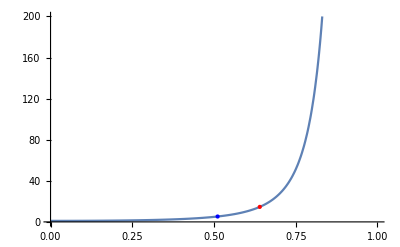

```mathematica
Show[
Plot[smaf[e],{e, 0, 0.95}, PlotRange->{{0,1},{0,200}}],
Graphics[{PointSize[Large],Red,Point[{0.64,smaf[0.64]}]}],
Graphics[{PointSize[Large],Blue,Point[{0.511,smaf[0.511]}]}],
Graphics[{PointSize[Large],Green,Point[{0.9332,smaf[0.9332]}]}]
]
```

```mathematica
{smaf[0.64],smaf[0.511],smaf[0.9332]}
```

{14.6116,5.25036,5092.59}

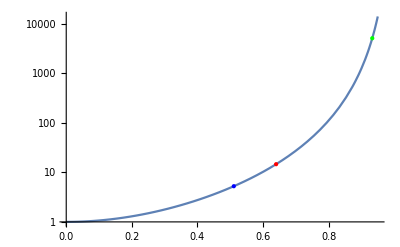

```mathematica
Show[
LogPlot[smaf[e],{e, 0, 0.95}, GridLines->Automatic],
Graphics[{PointSize[Large],Red,Point[{0.64,Log[smaf[0.64]]}]}],
Graphics[{PointSize[Large],Blue,Point[{0.511,Log[smaf[0.511]]}]}],
Graphics[{PointSize[Large],Green,Point[{0.9332,Log[smaf[0.9332]]}]}]
]
```

```mathematica
Solve[smaf[u]==100.0,{u}]
```

{{u→-1.04567-0.199658 ⅈ},{u→-1.04567+0.199658 ⅈ},{u→-0.793955},{u→0.793955},{u→1.04567-0.199658 ⅈ},{u→1.04567+0.199658 ⅈ}}

Formulae for the frequencies of GW from eccentric orbits.
Peters and Mathew 1963, also using Maggiore page 184, and Amaro-Seoane Eqn. (9) plus.

```mathematica
(* Can Mathematica use underscores yet? Nope, the underscore should be used only to designate the type when dummy function vars. *)
(*aa_bb=23
aa_bb+=2 Error *)
```

```mathematica
??BesselJ
```

RowBox[{"BesselJ", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["z", "TI"]}], "]"}] gives the Bessel function of the first kind RowBox[{SubscriptBox[StyleBox["J", "TI"], StyleBox["n", "TI"]], "(", StyleBox["z", "TI"], ")"}].

Attributes[BesselJ]={Listable,NumericFunction,Protected,ReadProtected}

Maggiore Eqns. 4.94-95, small a_n and small b_n , n≠0 .  Fourier coefficients for x(t) and y(t), all orbital motion in the x-y plane.

```mathematica
jj = BesselJ[#1,#2]&;
sma[n_,e_, asmaj_]:=asmaj/n(jj[n-1,n*e]-jj[n+1,ne])(* n-freq mult/index, e-ecc, asmaj-semimajor axis *)
smb[n_,e_, asmaj_]:=asmaj/n(jj[n-1,n*e]-jj[n+1,ne])
```

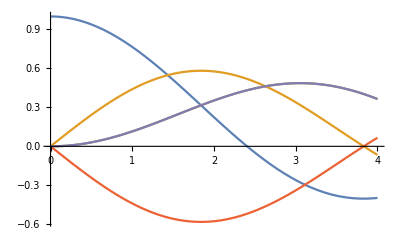

```mathematica
(* check the jj defn *)
Plot[{jj[0,u], jj[1,u], jj[2,u],jj[-1,u], jj[-2,u]},{u, 0, 4}]
```

Eqns. 4.99-101

```mathematica
bigA[n_,e_, asmaj_]:=asmaj^2/n(jj[n-2,n e]-jj[n+2,n e]-2 e jj[n-1,n e]+2 e jj[n+1,n e] )
bigB[n_,e_, asmaj_]:=(asmaj^2(1-e^2))/n(jj[n+2,n e]-jj[n-2,n e])
bigC[n_,e_, asmaj_]:=(asmaj^2 √(1-e^2))/n(jj[n+2,n e]+jj[n-2,n e]-e jj[n+1,n e]- e jj[n-1,n e] )
gg[n_,e_]:=n^6/(96 asmaj^4)(bigA[n,e,asmaj]^2+bigB[n,e,asmaj]^2+3 bigC[n,e,asmaj]^2-bigA[n,e,asmaj]*bigB[n,e,asmaj])/.asmaj->1  (* the asmaj's cancel out, same power in bigA^2 as in asmaj^4 *)
```

Check some limits, like e->0.  Then the peak frequency is at 2 ω_0, n=2.

```mathematica
{gg[2,0], gg[1,0.2], gg[1, 0.8]}
```

{1,0.00579633,0.0430687}

Plot Maggiore Fig. 4.8 (maybe), they are normalized to P for e=0 but what a?  Use a=1.

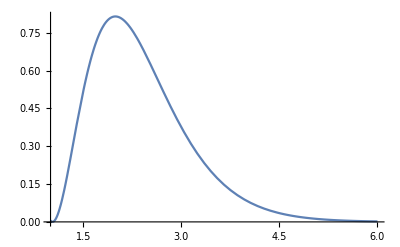

```mathematica
aplot=Plot[gg[n,0.2]/gg[2,0],{n, 1, 6}]
```

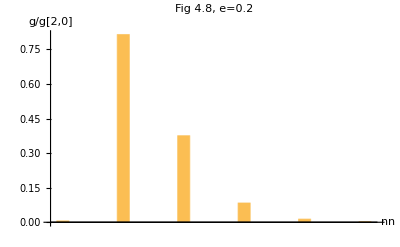

```mathematica
BarChart[ Table[
gg[n,0.2]/gg[2,0],{n, 1, 6}
],
BarSpacing->4, PlotLabel->"Fig 4.8, e=0.2",
AxesLabel->{"n", "g/g[2,0]"}]
```

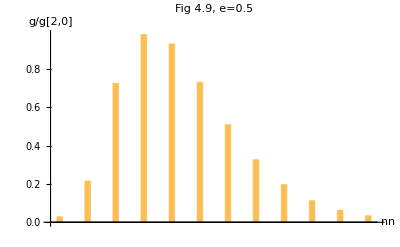

```mathematica
BarChart[ Table[
gg[n,0.5]/gg[2,0],{n, 1, 12}
],
BarSpacing->4,PlotLabel->"Fig 4.9, e=0.5",
AxesLabel->{"n", "g/g[2,0]"}]
```

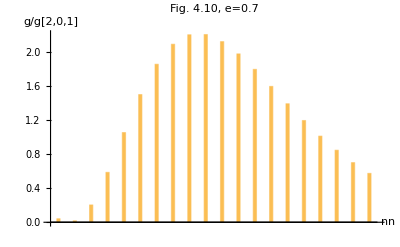

```mathematica
BarChart[ Table[
gg[n,0.7]/gg[2,0],{n, 1, 20}
],
BarSpacing->4, PlotLabel->"Fig. 4.10, e=0.7",
AxesLabel->{"n", "g/g[2,0,1]"}]
```

## Now the Caltech Confirmed Expolanets data.

I think the calculation should go, find the orbital frequency f_0 (Hz), from m_1, m_2, and a, then calculate the Power in front of total (Eqn 4.74) or of harmonic (Eqn. 4,107).

```mathematica
freq[m1_, m2_, a_]:=2π √((bigG(m1+m2))/a^3) (* Hz, orbital period *)
powerCoeff[m1_,m2_,a_]:=32 bigG^4 (m1^2 m2^2(m1+m2))/(5 cee^5 a^5) (* W, power radiated into n-th mode, if times g(n,e) or total if times f(n,e) *)
```

```mathematica
shortList = {alldata[[rowHeaders]]}~Join~alldata[[rowDataStart;;rowDataStart+10]];
shortList//MatrixForm
```

(pl_hostname | pl_letter | pl_discmethod | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
HD 142022 A | b | Radial Velocity | 1928. | 3.03 | 0.53 | 5.1 | 35.87 | 0.99 | 2014-05-14 | 27.88
HD 39091 | b | Radial Velocity | 2151. | 3.38 | 0.6405 | 10.27 | 18.21 | 1.1 | 2014-07-23 | 54.92
HD 137388 A | b | Radial Velocity | 330. | 0.89 | 0.36 | 0.223 | 38.45 | 0.86 | 2014-05-14 | 26.01
GJ 3021 | b | Radial Velocity | 133.71 | 0.49 | 0.511 | 3.37 | 17.62 | 0.9 | 2014-05-14 | 56.76
HD 63454 | b | Radial Velocity | 2.81805 | 0.0368 | 0. | 0.398 | 35.8 | 0.84 | 2015-03-26 | 27.93
HD 212301 | b | Radial Velocity | 2.24572 | 0.036 | 0. | 0.45 | 52.72 | 1.27 | 2014-05-14 | 18.97
CHXR 73 | b | Imaging |  | 210. |  | 12.569 |  | 0.35 | 2014-05-14 | 
CT Cha | b | Imaging |  | 440. |  | 17. | 165. |  | 2014-05-14 | 
HD 196067 | b | Radial Velocity | 3638. | 5.02 | 0.66 | 6.9 | 43.57 | 1.29 | 2014-05-14 | 22.95
HD 38283 | b | Radial Velocity | 363.2 | 1.02 | 0.41 | 0.34 | 37.78 | 1.08 | 2015-09-10 | 26.47
HD 131664 | b | Radial Velocity | 1951. | 3.17 | 0.638 | 18.15 | 57.21 | 1.1 | 2014-05-14 | 17.48)

```mathematica
{cols["pl_orbeccen"], cols["pl_bmassj"]}
```

{6,7}

Testing the Sort[] function on the short list.

```mathematica
Sort[shortList, #1[[cols["pl_orbeccen"] ]]>#2[[cols["pl_orbeccen"] ]]&  ]//MatrixForm
```

(pl_hostname | pl_letter | pl_discmethod | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
HD 39091 | b | Radial Velocity | 2151. | 3.38 | 0.6405 | 10.27 | 18.21 | 1.1 | 2014-07-23 | 54.92
HD 142022 A | b | Radial Velocity | 1928. | 3.03 | 0.53 | 5.1 | 35.87 | 0.99 | 2014-05-14 | 27.88
GJ 3021 | b | Radial Velocity | 133.71 | 0.49 | 0.511 | 3.37 | 17.62 | 0.9 | 2014-05-14 | 56.76
HD 137388 A | b | Radial Velocity | 330. | 0.89 | 0.36 | 0.223 | 38.45 | 0.86 | 2014-05-14 | 26.01
HD 212301 | b | Radial Velocity | 2.24572 | 0.036 | 0. | 0.45 | 52.72 | 1.27 | 2014-05-14 | 18.97
HD 63454 | b | Radial Velocity | 2.81805 | 0.0368 | 0. | 0.398 | 35.8 | 0.84 | 2015-03-26 | 27.93
CHXR 73 | b | Imaging |  | 210. |  | 12.569 |  | 0.35 | 2014-05-14 | 
CT Cha | b | Imaging |  | 440. |  | 17. | 165. |  | 2014-05-14 | 
HD 196067 | b | Radial Velocity | 3638. | 5.02 | 0.66 | 6.9 | 43.57 | 1.29 | 2014-05-14 | 22.95
HD 131664 | b | Radial Velocity | 1951. | 3.17 | 0.638 | 18.15 | 57.21 | 1.1 | 2014-05-14 | 17.48
HD 38283 | b | Radial Velocity | 363.2 | 1.02 | 0.41 | 0.34 | 37.78 | 1.08 | 2015-09-10 | 26.47)

Some of the fields are blank, so drop those planets from consideration.

```mathematica
Clear[filterBlanks2]
filterBlanks2[aa_, filterInd_]:=Module[{retList, blankList},
retList={};
blankList={};
For[i=1,i<=Length[aa], i++,
If[ NumberQ[ aa[[i,filterInd]] ], AppendTo[retList, aa[[i]] ], AppendTo[blankList, aa[[i]] ]]
];
{retList, blankList}
]
```

```mathematica
{alldata[[rowHeaders]]}~Join~filterBlanks2[shortList, cols["pl_orbeccen"] ][[1]]//MatrixForm (* the non-blanks *)
```

(pl_hostname | pl_letter | pl_discmethod | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
HD 142022 A | b | Radial Velocity | 1928. | 3.03 | 0.53 | 5.1 | 35.87 | 0.99 | 2014-05-14 | 27.88
HD 39091 | b | Radial Velocity | 2151. | 3.38 | 0.6405 | 10.27 | 18.21 | 1.1 | 2014-07-23 | 54.92
HD 137388 A | b | Radial Velocity | 330. | 0.89 | 0.36 | 0.223 | 38.45 | 0.86 | 2014-05-14 | 26.01
GJ 3021 | b | Radial Velocity | 133.71 | 0.49 | 0.511 | 3.37 | 17.62 | 0.9 | 2014-05-14 | 56.76
HD 63454 | b | Radial Velocity | 2.81805 | 0.0368 | 0. | 0.398 | 35.8 | 0.84 | 2015-03-26 | 27.93
HD 212301 | b | Radial Velocity | 2.24572 | 0.036 | 0. | 0.45 | 52.72 | 1.27 | 2014-05-14 | 18.97
HD 196067 | b | Radial Velocity | 3638. | 5.02 | 0.66 | 6.9 | 43.57 | 1.29 | 2014-05-14 | 22.95
HD 38283 | b | Radial Velocity | 363.2 | 1.02 | 0.41 | 0.34 | 37.78 | 1.08 | 2015-09-10 | 26.47
HD 131664 | b | Radial Velocity | 1951. | 3.17 | 0.638 | 18.15 | 57.21 | 1.1 | 2014-05-14 | 17.48)

```mathematica
{alldata[[rowHeaders]]}~Join~filterBlanks2[shortList, cols["pl_orbeccen"] ][[2]]//MatrixForm (* the blanks *)
```

(pl_hostname | pl_letter | pl_discmethod | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
pl_hostname | pl_letter | pl_discmethod | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
CHXR 73 | b | Imaging |  | 210. |  | 12.569 |  | 0.35 | 2014-05-14 | 
CT Cha | b | Imaging |  | 440. |  | 17. | 165. |  | 2014-05-14 | )

Filter the blanks in all masses, eccentricity, semimajor axis, and distance.

```mathematica
Print["Length alldata ",Length[alldata] ]
fdata1 = filterBlanks2[alldata[[rowDataStart;;]], cols["pl_orbeccen"] ][[1]]; Print[ "pl_orbeccen ", Length[fdata1]]
fdata2 = filterBlanks2[fdata1, cols["pl_orbper"] ][[1]]; Print[ "pl_orbper ",Length[fdata2] ]
fdata3 = filterBlanks2[fdata2, cols["pl_orbsmax"] ][[1]]; Print["pl_orbsmax ",Length[fdata3] ]
fdata4 = filterBlanks2[fdata3, cols["pl_bmassj"] ][[1]]; Print["pl_bmassj ",Length[fdata4] ] (* use pl_bmassj not pl_massj *)
fdata5 = filterBlanks2[fdata4, cols["st_dist"] ][[1]]; Print["st_dist ",Length[fdata5] ]
fdata6 = filterBlanks2[fdata5, cols["st_mass"] ][[1]]; Print["st_mass ",Length[fdata6] ]
```

Length alldata 3388

pl_orbeccen 984

pl_orbper 984

pl_orbsmax 930

pl_bmassj 887

st_dist 802

st_mass 766

```mathematica
{alldata[[rowHeaders]]}~Join~fdata6[[10;;14]]//MatrixForm
```

(pl_hostname | pl_letter | pl_discmethod | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
HD 108341 | b | Radial Velocity | 1129. | 2. | 0.85 | 3.5 | 49.4 | 0.84 | 2015-01-08 | 20.23
HD 216437 | b | Radial Velocity | 1256. | 2.32 | 0.29 | 1.82 | 26.52 | 1.15 | 2015-04-24 | 37.71
WASP-126 | b | Transit | 3.2888 | 0.0449 | 0.18 | 0.28 | 234. | 1.12 | 2016-05-05 | 
HD 111232 | b | Radial Velocity | 1143. | 1.97 | 0.2 | 6.8 | 28.88 | 0.78 | 2014-08-21 | 34.63
HD 11977 | b | Radial Velocity | 711. | 1.93 | 0.4 | 6.54 | 66.49 | 1.91 | 2014-05-14 | 15.04)

```mathematica
(*{alldata[[rowHeaders]]}~Join~fdata6//MatrixForm*)
```

```mathematica
{738/3269., Length[fdata6]/Length[alldata]}
```

{0.225757,383/1694}

Only 738/3269= 0.23, 23% have all the data fields I am about to use.  Maybe there is some minimal set, the fields are not all independent and Kepler’s laws might be used to infer the missing data.  For now use the “fdata6.”

```mathematica
pwrTot[m1_,m2_,asmaj_]:=32 bigG^4 ((m1 m2)^2(m1+m2))/(5 cee^5 asmaj^5)  (* W, Lead coefficient in eqn. 4.74 for total power radiated from orbiting masses in an eccentric orbit. *)
pwrSubN[m1_,m2_,asmaj_]:=pwrTot[m1,m2,asmaj]  (* Lead coefficient for eqn. 4.107, power in nth harmonic. *)
```

## The three formulae, Peters & Mathews eqn (20), Amaro-Seone et al. (4)-(6), and Maggiore (4.107-108). Check that they are the same. Similar looking and Bessel funtion identities might make them identical...one hopes.

Already have Maggiore’s formula above, gg[n_,e_,asmaj_].
Peters and Mathews, eqn 20.  The coefficient on eqn 19 is the same as in Maggiore.

```mathematica
ggPM[n_,e_]:= n^4/32( (jj[n-2,n e]-2 e jj[n-1,n e]+2/n jj[n, n e]+2 e jj[n+1, n e]-jj[n+2, n e])^2+
(1-e^2)(jj[n-2,n e]-2 jj[n, n e]+jj[n+2, n e])^2 +4/(3 n^2)jj[n, n e]^2 )
```

Amaro-Seone et al.

```mathematica
bigAAS[n_,e_]:=jj[n-2,n e]-2 jj[n, n e]+jj[n+2,n e]
bigBAS[n_,e_]:=jj[n-2,n e]-2 e jj[n-1,n e]+2/n jj[n,n e]+2 e jj[n+1,n e]-jj[n+2,n e]
ggAS[n_, e_]:=n^4/32(bigBAS[n,e]^2 + (1-e^2)bigAAS[n,e]^2+4/(3 n^2)jj[n,n e]^2)
```

```mathematica
Table[
ggPM[n,0.2]/ggPM[2,0],{n, 1, 6}
]
```

{0.00579633,0.814184,0.37536,0.0835568,0.0136303,0.00186696}

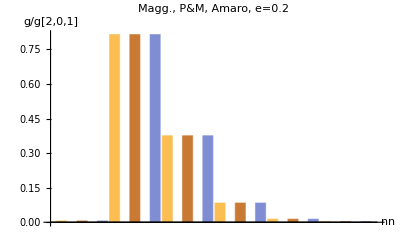

```mathematica
abar=BarChart[ Table[
{gg[n,0.2]/gg[2,0],ggPM[n,0.2]/ggPM[2,0],ggAS[n,0.2]/ggAS[2,0]},{n, 1, 6}
],
BarSpacing->1,PlotLabel->"Magg., P&M, Amaro, e=0.2",
AxesLabel->{"n", "g/g[2,0,1]"}]
```

```mathematica
(*Export[myDir<>"g_ecc0p2.png",abar,"PNG", ImageSize→{11,8.5}*72]*)
```

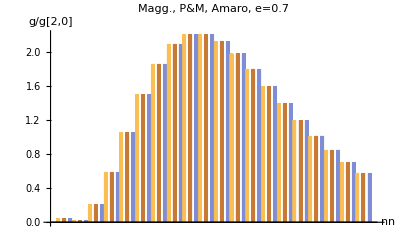

```mathematica
bbar=BarChart[ Table[
{gg[n,0.7]/gg[2,0],ggPM[n,0.7]/ggPM[2,0],ggAS[n,0.7]/ggAS[2,0]},{n, 1,20}
],
BarSpacing->1, PlotLabel->"Magg., P&M, Amaro, e=0.7",
AxesLabel->{"n", "g/g[2,0]"}]
```

```mathematica
(*Export[myDir<>"g_ecc0p7.png",bbar,"PNG", ImageSize→{11,8.5}*72]*)
```

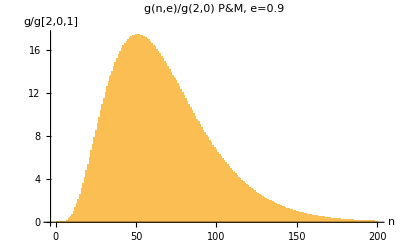

```mathematica
ecc=0.9;
cbar=
Show[
BarChart[ Table[
ggPM[n,ecc]/ggPM[2,0],{n, 1,200}
],
Axes->None,
Ticks->Automatic,
BarSpacing->1, PlotLabel->StringForm["g(n,e)/g(2,0) P&M, e=``",ecc],
AxesLabel->{"n", "g/g[2,0,1]"}
],
Axes->True,
Ticks->Automatic
]
fileString = myDir<>"gPM_ecc0p"<>ToString[Floor[ecc*10]]<>".png" ;
(*Export[fileString, cbar, "PNG", ImageSize->{11,8.5}*72]*)
```

Playing with strings.

```mathematica
myDir<>"gPM_ecc0p"<>ToString[ Floor[ecc*10] ]<>".png"
```

/home/gabella/Documents/astro/exop/gPM_ecc0p9.png

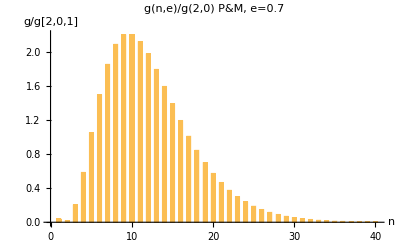

```mathematica
ecc=0.7;
dbar=
Show[
BarChart[ Table[
ggPM[n,ecc]/ggPM[2,0],{n, 1,40}
],
Axes->None,
Ticks->Automatic,
BarSpacing->1, PlotLabel->StringForm["g(n,e)/g(2,0) P&M, e=``",ecc],
AxesLabel->{"n", "g/g[2,0,1]"}
],
Axes->True,
Ticks->Automatic
]
fileString = myDir<>"gPM_ecc0p"<>ToString[Floor[ecc*10]]<>".png" ;
(*Export[fileString, dbar, "PNG", ImageSize->{11,8.5}*72]*)
```

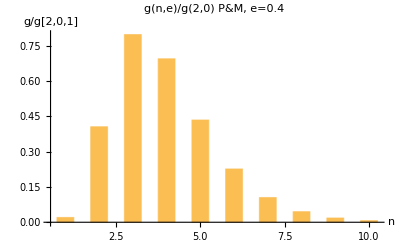

```mathematica
ecc=0.4;
ebar=
Show[
BarChart[ Table[
ggPM[n,ecc]/ggPM[2,0],{n, 1,10}
],
Axes->None,
Ticks->Automatic,
BarSpacing->1, PlotLabel->StringForm["g(n,e)/g(2,0) P&M, e=``",ecc],
AxesLabel->{"n", "g/g[2,0,1]"}
],
Axes->True,
Ticks->Automatic
]
fileString = myDir<>"gPM_ecc0p"<>ToString[Floor[ecc*10]]<>".png" ;
(*Export[fileString, ebar, "PNG", ImageSize->{11,8.5}*72]*)
```

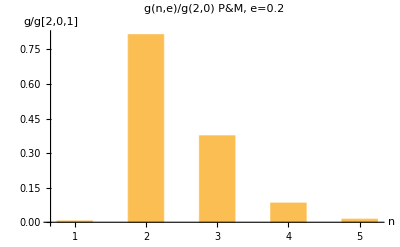

```mathematica
ecc=0.2;
fbar=
Show[
BarChart[ Table[
ggPM[n,ecc]/ggPM[2,0],{n, 1,5}
],
Axes->None,
Ticks->Automatic,
BarSpacing->1, PlotLabel->StringForm["g(n,e)/g(2,0) P&M, e=``",ecc],
AxesLabel->{"n", "g/g[2,0,1]"}
],
Axes->True,
Ticks->Automatic
]
fileString = myDir<>"gPM_ecc0p"<>ToString[Floor[ecc*10]]<>".png" ;
(*Export[fileString, fbar, "PNG", ImageSize->{11,8.5}*72]*)
```

## Estimate max frequency harmonic n given the eccentricity e.

```mathematica
??ggPM
```

Global`ggPM

ggPM[n_,e_]:=1/32 n^4 ((jj[n-2,n e]-2 e jj[n-1,n e]+(2 jj[n,n e])/n+2 e jj[n+1,n e]-jj[n+2,n e])^2+(1-e^2) (jj[n-2,n e]-2 jj[n,n e]+jj[n+2,n e])^2+(4 jj[n,n e]^2)/(3 n^2))

```mathematica
jj[-1,0]
```

0

```mathematica
ggPM[1,0.0]
```

0.

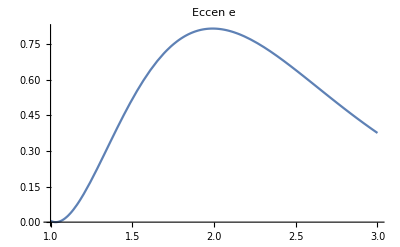

```mathematica
Plot[ggPM[n,e]/ggPM[2,0]/.e->0.2,{n, 1, 3}, PlotRange->All,PlotLabel->"Eccen "<>ToString[e]]
```

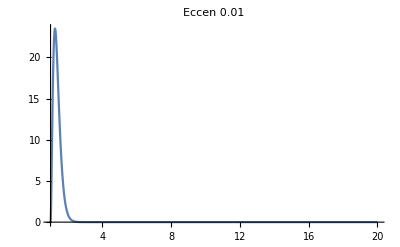
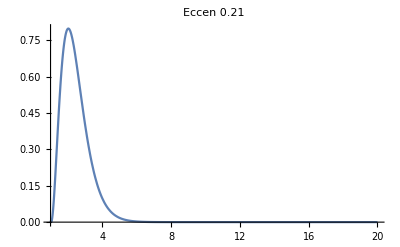
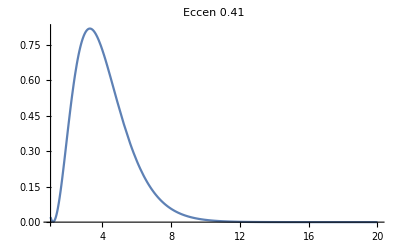
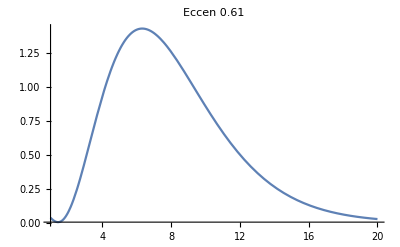

```mathematica
Table[
Plot[ggPM[n,e] /ggPM[2,0] ,{n, 1, 20}, PlotRange->All,PlotLabel->"Eccen "<>ToString[e]],{e, 0.01, 0.8, 0.2}
]
```

```mathematica
(*Table[
{n,e,ggPM[n,e]/ggPM[2,0]},{n, 1, 20},{e, 0, 0.8, 0.2}
]*)
```

```mathematica
{ggPM[2,0.7], ggPM[2,0]}
```

{0.0167665,1}

Looking for ways to search for the second, tail decrease below some threshold.

```mathematica
(* NSolve[ggPM[nn,0.7]==0.05&&nn>2,nn, Reals] *)
aa=Table[{nn,ggPM[nn,0.7], ggPM[nn,0.7]<0.05},{nn,1,40}]
(* So, 30, 0.05498 and then 31, 0.04238, puts 0.05 around n = 30+(31-30)/(0.0428-0.05498)*(0.05-0.05498)   *)
```

{{1,0.0413106,True},{2,0.0167665,True},{3,0.203845,False},{4,0.587497,False},{5,1.05607,False},{6,1.5034,False},{7,1.86036,False},{8,2.09591,False},{9,2.20752,False},{10,2.21008,False},{11,2.12669,False},{12,1.98238,False},{13,1.80025,False},{14,1.59957,False},{15,1.39521,False},{16,1.19775,False},{17,1.01415,False},{18,0.848358,False},{19,0.702122,False},{20,0.575587,False},{21,0.467848,False},{22,0.377364,False},{23,0.302269,False},{24,0.240588,False},{25,0.190388,False},{26,0.149865,False},{27,0.117391,False},{28,0.0915389,False},{29,0.071082,False},{30,0.0549824,False},{31,0.0423754,True},{32,0.0325487,True},{33,0.0249217,True},{34,0.0190253,True},{35,0.0144835,True},{36,0.0109969,True},{37,0.00832899,True},{38,0.00629355,True},{39,0.004745,True},{40,0.00356996,True}}

```mathematica
nstar=30+(31-30)/(aa[[31,2]]-aa[[30,2]])*(0.05-aa[[30,2]]) (* linear interpolation to find the 0.05 point*)
```

30.3952

```mathematica
{ggPM[Floor[nstar],0.7],ggPM[nstar,0.7],ggPM[Ceiling[nstar],0.7]}
```

{0.0549824,0.0496254,0.0423754}

```mathematica
(* A local equation solver, but NSolve is a global one. *)
FindRoot[ggPM[nn,0.7]==0.05,{nn,20}]
```

{nn→30.3663}

More elaborate search for the second root, where the curve is coming down toward 0.

```mathematica
Clear[findSecondRoot];
findSecondRoot[ee_, lim_]:=Module[{alist,nmax=200,iloop=True, ifirstRoot=False, ii, prev},
alist=Table[{ii,ggPM[ii,ee]-lim>0 },{ii, 1, nmax}];  (* Check for neg, then pos, then neg, there is second root. *)
ii=1;
prev=alist[[ii,2]];
While[iloop,
If[ Xor[prev,alist[[ii,2]]],
If[ifirstRoot==False,ifirstRoot=True, iloop=False ], ];(* True when goes from neg to pos in above ggPM-lim. *)
prev = alist[[ii,2]];
ii++;
];
(* Now ii is near second root. *)
FindRoot[ggPM[nn,ee]-lim==0,{nn,ii}]
]
```

```mathematica
ggPM[2.31616,0.7]
```

0.0499993

```mathematica
findSecondRoot[0.7,0.05]
```

{nn→30.3663}

```mathematica
ee=Range[0.1,0.9,0.05];
maxNdata=Table[
{ee[[i]],findSecondRoot[ee[[i]], 0.05]},{i,1,Length[ee]}
]
```

{{0.1,{nn→3.28484}},{0.15,{nn→3.75374}},{0.2,{nn→4.29642}},{0.25,{nn→4.9412}},{0.3,{nn→5.72119}},{0.35,{nn→6.67979}},{0.4,{nn→7.87705}},{0.45,{nn→9.39924}},{0.5,{nn→11.3747}},{0.55,{nn→14.0019}},{0.6,{nn→17.6017}},{0.65,{nn→22.7222}},{0.7,{nn→30.3663}},{0.75,{nn→42.5429}},{0.8,{nn→63.8058}},{0.85,{nn→106.539}},{0.9,{nn→4.76851}}}

The trouble above is that e=0.9 has a second root at nn=4.8 and the third root is really of interest to us.

```mathematica
{maxNdata[[1,1]], maxNdata[[1,2, 1,2]]}
```

{0.1,3.28484}

```mathematica
maxNdata2 = Table[
{maxNdata[[i,1]],maxNdata[[i,2,1,2]]},{i, 1, Length[maxNdata]}
](* eccentricity 0.9 is trouble because of the rise and fall at the start.  *)
```

{{0.1,3.28484},{0.15,3.75374},{0.2,4.29642},{0.25,4.9412},{0.3,5.72119},{0.35,6.67979},{0.4,7.87705},{0.45,9.39924},{0.5,11.3747},{0.55,14.0019},{0.6,17.6017},{0.65,22.7222},{0.7,30.3663},{0.75,42.5429},{0.8,63.8058},{0.85,106.539},{0.9,4.76851}}

Fix the high eccentricity point by hand.

```mathematica
FindRoot[ggPM[nn,0.9]-0.05==0,{nn,190}]
```

{nn→216.182}

```mathematica
maxNdata2[[17]]
```

{0.9,4.76851}

```mathematica
maxNdata3=ReplacePart[maxNdata2,17->{0.9,216.182}]
```

{{0.1,3.28484},{0.15,3.75374},{0.2,4.29642},{0.25,4.9412},{0.3,5.72119},{0.35,6.67979},{0.4,7.87705},{0.45,9.39924},{0.5,11.3747},{0.55,14.0019},{0.6,17.6017},{0.65,22.7222},{0.7,30.3663},{0.75,42.5429},{0.8,63.8058},{0.85,106.539},{0.9,216.182}}

```mathematica
(*fitEcc2N = Fit[maxNdata3, {1,x,x^2, x^3},x]*) (* This does not work well at all. *)
```

```mathematica
fitEcc2N2 = NonlinearModelFit[maxNdata3,(a+b x +c x^2)Exp[d x],{a,b,c,d},x]
```

FittedModel[ⅇ^(9.52122 x) (0.589993-1.41301 x+0.892102 x^2)]

```mathematica
ecc2n=Normal[fitEcc2N2]
```

ⅇ^(9.52122 x) (0.589993-1.41301 x+0.892102 x^2)

```mathematica
ecc2n/.x->0.4
```

7.55246

```mathematica
{fitEcc2N2[0.0],fitEcc2N2[0.4],fitEcc2N2[0.9], fitEcc2N2[0.99]}
```

{0.589993,7.55246,215.34,812.225}

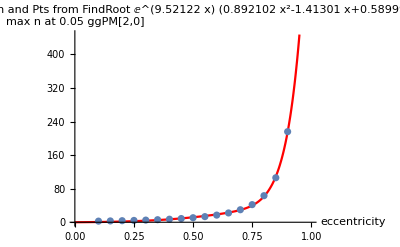

```mathematica
aeccPlot=Show[{
Plot[fitEcc2N2[x],{x, 0, 0.95}, PlotRange->{{0,1},All},PlotStyle->{RGBColor[1,0,0]},
PlotLabel->"Fit Fcn and Pts from FindRoot\n"ecc2n, AxesLabel->{"eccentricity","max n at 0.05 ggPM[2,0]"}],
ListPlot[ maxNdata3, PlotRange->{{0,1},All}, PlotLabel->"From FindRoot"]
(*Plot[fitEcc2N,{x,0,0.9}]*)
}]
```

```mathematica
(*Export[myDir<>"nMaxFromEcc.png",aeccPlot,"PNG", ImageSize→{11,8.5}*72]*)
```

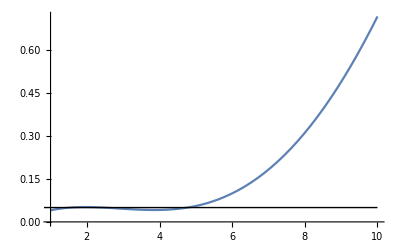

```mathematica
Show[{
Plot[ggPM[nn,0.9],{nn,1,10}],
Graphics[Line[{{0, 0.05},{10,0.05}}]  ]
}]
```

## Amaro-Seoane et al. Eqn. (9) and (10) toward Strain Sensitivity hf.

h_n Eqn. (9).

```mathematica
Clear[chirpM,redM, totM, fr, hh]
chirpM[m1_,m2_]:=(m1 m2)^(3/5)/(m1+m2)^(1/5)
redM[m1_,m2_]:=(m1 m2)/(m1+m2)
totM[m1_,m2_]:=m1+m2
fr[m1_,m2_,a_]:=1/(2 π)√((bigG(m1+m2))/a^3)
hh [n_,e_,m1_,m2_,a_, dL_]:= bigG^(5/3)/cee^4 2 √(32/5)chirpM[m1,m2]^(5/3)/(n dL)(2π fr[m1,m2,a])^(2/3) √ggAS[n,e]  (* Subscript[d, L] is luminosity distance d=Subscript[d, L]/(1+z), z=0 for us, Subscript[f, r] is orbital freq *)
```

```mathematica
shortList//TableForm
```

pl_hostname | pl_letter | pl_discmethod | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
HD 142022 A | b | Radial Velocity | 1928. | 3.03 | 0.53 | 5.1 | 35.87 | 0.99 | 2014-05-14 | 27.88
HD 39091 | b | Radial Velocity | 2151. | 3.38 | 0.6405 | 10.27 | 18.21 | 1.1 | 2014-07-23 | 54.92
HD 137388 A | b | Radial Velocity | 330. | 0.89 | 0.36 | 0.223 | 38.45 | 0.86 | 2014-05-14 | 26.01
GJ 3021 | b | Radial Velocity | 133.71 | 0.49 | 0.511 | 3.37 | 17.62 | 0.9 | 2014-05-14 | 56.76
HD 63454 | b | Radial Velocity | 2.81805 | 0.0368 | 0. | 0.398 | 35.8 | 0.84 | 2015-03-26 | 27.93
HD 212301 | b | Radial Velocity | 2.24572 | 0.036 | 0. | 0.45 | 52.72 | 1.27 | 2014-05-14 | 18.97
CHXR 73 | b | Imaging |  | 210. |  | 12.569 |  | 0.35 | 2014-05-14 | 
CT Cha | b | Imaging |  | 440. |  | 17. | 165. |  | 2014-05-14 | 
HD 196067 | b | Radial Velocity | 3638. | 5.02 | 0.66 | 6.9 | 43.57 | 1.29 | 2014-05-14 | 22.95
HD 38283 | b | Radial Velocity | 363.2 | 1.02 | 0.41 | 0.34 | 37.78 | 1.08 | 2015-09-10 | 26.47
HD 131664 | b | Radial Velocity | 1951. | 3.17 | 0.638 | 18.15 | 57.21 | 1.1 | 2014-05-14 | 17.48

```mathematica
{shortList[[1]]}~Join~shortList[[2;;5]]//TableForm
```

pl_hostname | pl_letter | pl_discmethod | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
HD 142022 A | b | Radial Velocity | 1928. | 3.03 | 0.53 | 5.1 | 35.87 | 0.99 | 2014-05-14 | 27.88
HD 39091 | b | Radial Velocity | 2151. | 3.38 | 0.6405 | 10.27 | 18.21 | 1.1 | 2014-07-23 | 54.92
HD 137388 A | b | Radial Velocity | 330. | 0.89 | 0.36 | 0.223 | 38.45 | 0.86 | 2014-05-14 | 26.01
GJ 3021 | b | Radial Velocity | 133.71 | 0.49 | 0.511 | 3.37 | 17.62 | 0.9 | 2014-05-14 | 56.76

```mathematica
Clear[aNmax];
aNmax[ecc_]:=If[ecc==0, 2, Floor[fitEcc2N2[ecc]+1]]
Clear[aNmin];
aNmin[ecc_]:=If[ecc==0,1, 1]
```

Test the above formulae on this short table.

Create string names without the underscore and with an "a" in front!  Later make them an expression (symbol?) so they can hold the data.

stuff

```mathematica
colNamesStr=Module[{aa, bb, myname},
aa=alldata[[rowHeaders]];
bb={};
For[ii=1, ii≤Length[aa], ii++,
myname="a"<>StringReplace[aa[[ii]],"_"->""];
AppendTo[bb, myname  ]
];
bb
]
```

{aplhostname,aplletter,apldiscmethod,aplorbper,aplorbsmax,aplorbeccen,aplbmassj,astdist,astmass,arowupdate,astplx}

```mathematica
(* Test above. Not working with String names as list Names. *)
(*Remove[colNames, aplhostname,apldiscmethod, aplorbper,aplorbsmax,aplorbeccen,aplbmassj,astdist,astmass,arowupdate,astplx]*)
bdata = shortList[[2;;5]]
colNames=Transpose[ bdata ];
{aplhostname,aplletter,apldiscmethod, aplorbper,aplorbsmax,aplorbeccen,aplbmassj,astdist,astmass,arowupdate,astplx}=Transpose[ bdata ];
colNames[[cols["pl_hostname"]]]
colNames[[cols["pl_bmassj"]]]
aplorbper
astdist
```

{{HD 142022 A,b,Radial Velocity,1928.,3.03,0.53,5.1,35.87,0.99,2014-05-14,27.88},{HD 39091,b,Radial Velocity,2151.,3.38,0.6405,10.27,18.21,1.1,2014-07-23,54.92},{HD 137388 A,b,Radial Velocity,330.,0.89,0.36,0.223,38.45,0.86,2014-05-14,26.01},{GJ 3021,b,Radial Velocity,133.71,0.49,0.511,3.37,17.62,0.9,2014-05-14,56.76}}

{HD 142022 A,HD 39091,HD 137388 A,GJ 3021}

{5.1,10.27,0.223,3.37}

{1928.,2151.,330.,133.71}

{35.87,18.21,38.45,17.62}

```mathematica
(* Create a list of eccen, {{freq(Hz)_1, h_1},{freq_2, h_2}....}  *)
 atab=Table[
{bdata[[nn,cols["pl_orbeccen"] ]], 
Table[
Module[{afr},
afr = fr[aplbmassj[[nn]]*massJs*massSun, astmass[[nn]]*massSun, aplorbsmax[[nn]]*au];
{pp*afr, hh [pp,aplorbeccen[[nn]],aplbmassj[[nn]]*massJs*massSun,astmass[[nn]]*massSun,aplorbsmax[[nn]]*au, astdist[[nn]]*pc]}
], {pp,1,Max[ {aNmax[ aplorbeccen[[nn]] ], 3}] }
]},
{nn, 1, Length[bdata]}
];
atab//TableForm
```

0.53 | 5.99455×10^-9 | 1.87098×10^-26
1.19891×10^-8 | 2.17487×10^-26
1.79836×10^-8 | 2.88323×10^-26
2.39782×10^-8 | 2.66585×10^-26
2.99727×10^-8 | 2.19441×10^-26
3.59673×10^-8 | 1.70757×10^-26
4.19618×10^-8 | 1.2859×10^-26
4.79564×10^-8 | 9.4794×10^-27
5.39509×10^-8 | 6.88467×10^-27
5.99455×10^-8 | 4.94559×10^-27
6.594×10^-8 | 3.52291×10^-27
7.19345×10^-8 | 2.49289×10^-27
7.79291×10^-8 | 1.75458×10^-27
8.39236×10^-8 | 1.22948×10^-27
8.99182×10^-8 | 8.58338×10^-28
0.6405 | 5.37385×10^-9 | 8.23435×10^-26
1.07477×10^-8 | 4.50948×10^-26
1.61216×10^-8 | 8.43126×10^-26
2.14954×10^-8 | 9.56102×10^-26
2.68693×10^-8 | 9.39107×10^-26
3.22431×10^-8 | 8.63408×10^-26
3.7617×10^-8 | 7.64652×10^-26
4.29908×10^-8 | 6.61219×10^-26
4.83647×10^-8 | 5.62442×10^-26
5.37385×10^-8 | 4.72716×10^-26
5.91124×10^-8 | 3.93701×10^-26
6.44862×10^-8 | 3.25559×10^-26
6.98601×10^-8 | 2.67671×10^-26
7.52339×10^-8 | 2.19041×10^-26
8.06078×10^-8 | 1.78541×10^-26
8.59816×10^-8 | 1.45046×10^-26
9.13555×10^-8 | 1.17498×10^-26
9.67293×10^-8 | 9.49465×10^-27
1.02103×10^-7 | 7.65571×10^-27
1.07477×10^-7 | 6.16115×10^-27
1.12851×10^-7 | 4.94994×10^-27
1.18225×10^-7 | 3.9708×10^-27
1.23599×10^-7 | 3.18099×10^-27
0.36 | 3.50151×10^-8 | 1.67249×10^-27
7.00302×10^-8 | 4.48259×10^-27
1.05045×10^-7 | 3.73082×10^-27
1.4006×10^-7 | 2.35543×10^-27
1.75075×10^-7 | 1.3482×10^-27
2.1009×10^-7 | 7.34517×10^-28
2.45106×10^-7 | 3.88567×10^-28
0.511 | 8.78293×10^-8 | 1.38037×10^-25
1.75659×10^-7 | 1.78231×10^-25
2.63488×10^-7 | 2.24451×10^-25
3.51317×10^-7 | 2.00027×10^-25
4.39146×10^-7 | 1.59178×10^-25
5.26976×10^-7 | 1.19878×10^-25
6.14805×10^-7 | 8.74164×10^-26
7.02634×10^-7 | 6.24198×10^-26
7.90463×10^-7 | 4.39197×10^-26
8.78293×10^-7 | 3.05689×10^-26
9.66122×10^-7 | 2.11002×10^-26
1.05395×10^-6 | 1.44689×10^-26
1.14178×10^-6 | 9.86901×10^-27
1.22961×10^-6 | 6.702×10^-27

```mathematica
(*Remove[colNames,aplhostname,aplorbper,aplorbsmax,aplorbeccen,aplbmassj,astdist,astmass,arowupdate,astplx]*)
 bdata = fdata6; (* Data filtered to have non-null entries in the fields we want. *)
{aplhostname,aplletter,apldiscmethod,aplorbper,aplorbsmax,aplorbeccen,aplbmassj,astdist,astmass,arowupdate,astplx}=Transpose[ bdata ];
```

```mathematica
(* Create a list of eccen, {{freq(Hz)_1, h_1},{freq_2, h_2}....}  *)
 atab=Table[
{bdata[[nn,cols["pl_orbeccen"] ]], 
Table[
Module[{afr},
afr = fr[aplbmassj[[nn]]*massJs*massSun, astmass[[nn]]*massSun, aplorbsmax[[nn]]*au];
{pp*afr, hh [pp,aplorbeccen[[nn]],aplbmassj[[nn]]*massJs*massSun,astmass[[nn]]*massSun,aplorbsmax[[nn]]*au, astdist[[nn]]*pc]}
], {pp,1,Max[ {aNmax[ aplorbeccen[[nn]] ], 3}] }
]},
{nn, 1, Length[bdata]}
];
atab[[12;;16]]//TableForm
```

0.18 | 3.52638×10^-6 | 4.69165×10^-27
7.05275×10^-6 | 3.13897×10^-26
0.0000105791 | 1.27718×10^-26
0.2 | 1.01668×10^-8 | 1.62175×10^-26
2.03336×10^-8 | 9.61035×10^-26
3.05005×10^-8 | 4.35022×10^-26
0.4 | 1.63654×10^-8 | 3.17382×10^-26
3.27308×10^-8 | 7.08011×10^-26
4.90962×10^-8 | 6.6168×10^-26
6.54616×10^-8 | 4.6313×10^-26
8.1827×10^-8 | 2.93028×10^-26
9.81924×10^-8 | 1.76275×10^-26
1.14558×10^-7 | 1.02908×10^-26
1.30923×10^-7 | 5.89017×10^-27
0. | 2.9227×10^-6 | 0.
5.8454×10^-6 | 7.69367×10^-26
8.76809×10^-6 | 0.
0.28 | 1.19946×10^-8 | 2.58846×10^-27
2.39892×10^-8 | 1.00729×10^-26
3.59838×10^-8 | 6.43188×10^-27
4.79784×10^-8 | 3.17317×10^-27

```mathematica
{atab[[1]], atab[[3]]}
```

{{0.53,{{5.99455×10^-9,1.87098×10^-26},{1.19891×10^-8,2.17487×10^-26},{1.79836×10^-8,2.88323×10^-26},{2.39782×10^-8,2.66585×10^-26},{2.99727×10^-8,2.19441×10^-26},{3.59673×10^-8,1.70757×10^-26},{4.19618×10^-8,1.2859×10^-26},{4.79564×10^-8,9.4794×10^-27},{5.39509×10^-8,6.88467×10^-27},{5.99455×10^-8,4.94559×10^-27},{6.594×10^-8,3.52291×10^-27},{7.19345×10^-8,2.49289×10^-27},{7.79291×10^-8,1.75458×10^-27},{8.39236×10^-8,1.22948×10^-27},{8.99182×10^-8,8.58338×10^-28}}},{0.36,{{3.50151×10^-8,1.67249×10^-27},{7.00302×10^-8,4.48259×10^-27},{1.05045×10^-7,3.73082×10^-27},{1.4006×10^-7,2.35543×10^-27},{1.75075×10^-7,1.3482×10^-27},{2.1009×10^-7,7.34517×10^-28},{2.45106×10^-7,3.88567×10^-28}}}}

```mathematica
{atab[[1,2]], atab[[1,2, 1, 1]], atab[[1,2, 2, 1]],Length[  atab[[1,2]]  ]}
```

{{{5.99455×10^-9,1.87098×10^-26},{1.19891×10^-8,2.17487×10^-26},{1.79836×10^-8,2.88323×10^-26},{2.39782×10^-8,2.66585×10^-26},{2.99727×10^-8,2.19441×10^-26},{3.59673×10^-8,1.70757×10^-26},{4.19618×10^-8,1.2859×10^-26},{4.79564×10^-8,9.4794×10^-27},{5.39509×10^-8,6.88467×10^-27},{5.99455×10^-8,4.94559×10^-27},{6.594×10^-8,3.52291×10^-27},{7.19345×10^-8,2.49289×10^-27},{7.79291×10^-8,1.75458×10^-27},{8.39236×10^-8,1.22948×10^-27},{8.99182×10^-8,8.58338×10^-28}},5.99455×10^-9,1.19891×10^-8,15}

Make lists to plot freq vs eccen.

```mathematica
freqVecc = Table[
Table[
{atab[[ii,1]],atab[[ii,2,kk, 1]]},{kk, 1, Length[ atab[[ii,2]] ]}
],
{ii, 1, Length[atab]}
];

freqVecc[[1;;3]]
```

{{{0.53,5.99455×10^-9},{0.53,1.19891×10^-8},{0.53,1.79836×10^-8},{0.53,2.39782×10^-8},{0.53,2.99727×10^-8},{0.53,3.59673×10^-8},{0.53,4.19618×10^-8},{0.53,4.79564×10^-8},{0.53,5.39509×10^-8},{0.53,5.99455×10^-8},{0.53,6.594×10^-8},{0.53,7.19345×10^-8},{0.53,7.79291×10^-8},{0.53,8.39236×10^-8},{0.53,8.99182×10^-8}},{{0.6405,5.37385×10^-9},{0.6405,1.07477×10^-8},{0.6405,1.61216×10^-8},{0.6405,2.14954×10^-8},{0.6405,2.68693×10^-8},{0.6405,3.22431×10^-8},{0.6405,3.7617×10^-8},{0.6405,4.29908×10^-8},{0.6405,4.83647×10^-8},{0.6405,5.37385×10^-8},{0.6405,5.91124×10^-8},{0.6405,6.44862×10^-8},{0.6405,6.98601×10^-8},{0.6405,7.52339×10^-8},{0.6405,8.06078×10^-8},{0.6405,8.59816×10^-8},{0.6405,9.13555×10^-8},{0.6405,9.67293×10^-8},{0.6405,1.02103×10^-7},{0.6405,1.07477×10^-7},{0.6405,1.12851×10^-7},{0.6405,1.18225×10^-7},{0.6405,1.23599×10^-7}},{{0.36,3.50151×10^-8},{0.36,7.00302×10^-8},{0.36,1.05045×10^-7},{0.36,1.4006×10^-7},{0.36,1.75075×10^-7},{0.36,2.1009×10^-7},{0.36,2.45106×10^-7}}}

The total number of modes considered.

```mathematica
Sum[ Length[freqVecc[[i]]], {i, 1, Length[freqVecc]}]
```

5725

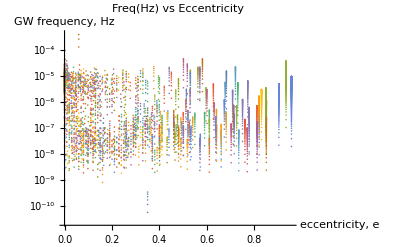

```mathematica
alogplot=ListLogPlot[freqVecc, 
PlotLabel->"Freq(Hz) vs Eccentricity",
AxesLabel->{"eccentricity, e", "GW frequency, Hz"}]
```

```mathematica
mylen=Length[atab]
```

766

```mathematica
fileString= myDir<>"freqVecc"<>ToString[mylen]<>"exopo.png";
Export[fileString, alogplot, "PNG", ImageSize->{11,8.5}*72]
```

/home/gabella/Documents/astro/exop/freqVecc766exopo.png

Now for the hf calculation following Amaro-Seoane et al.  Already have h with correct units (unitless) above.  Note the G^(5/3)/c^4~6.3×10^-55.  But for strain sensitivity, do the AS eqn. (10) enhancement,
 hobs,n = h_n  √(T f_(r n)) , where T is max(T_orb, T_obs), so that T f_(f n)= 1 or N_orbs, the latter if observed for many orbital periods.  So their formula is like a sqrt(N) incoherent addition of wave amplitudes.
 Used 3 years and 10 years for LISA observing T_obs...in previous exoplanet work (Hot Jupiters).

```mathematica
rootNfcn := Sqrt[ Max[ #1, #2]*#3/#1 ]&; (* #1 is Subscript[t, orb], #2 is Subscript[t, obs], same units!, #3 is the n of the harmonic, 2 for circular *)
```

```mathematica
rootNfcn[14002.,3*365.24, {1,2,3}]
```

{1.,1.41421,1.73205}

```mathematica
rootTab=Table[
Table[
{fdata6[[ii,cols["pl_orbper"]]],rootNfcn[fdata6[[ii,cols["pl_orbper"]]]*secsDay, 3*secsYear, kk]} ,{kk, 1, Length[ atab[[ii,2]] ]}
],
{ii, 1, Length[atab]}
];
rootTab[[12;;14]]
```

{{{3.2888,18.2529},{3.2888,25.8135},{3.2888,31.6149}},{{1143.,1.},{1143.,1.41421},{1143.,1.73205}},{{711.,1.24141},{711.,1.75562},{711.,2.15018},{711.,2.48282},{711.,2.77588},{711.,3.04082},{711.,3.28446},{711.,3.51124}}}

First just points and then
 “bin” the frequency.  Use AS et al.’s hobs,n and then multiply by Sqrt[T_obs].

```mathematica
{Length[atab], Length[fdata6]}  (* Should be in the same order too.  CHECK THIS! *)
```

{766,766}

```mathematica
{atab[[2,2,{1,2,3}, 1]], atab[[2,2]], Length[atab[[2,2]] ], fdata6[[2,cols["pl_orbper"]]],
rootNfcn[fdata6[[2,cols["pl_orbper"]]]*secsDay, 3*secsYear, {1,2,3}]}
```

{{5.37385×10^-9,1.07477×10^-8,1.61216×10^-8},{{5.37385×10^-9,8.23435×10^-26},{1.07477×10^-8,4.50948×10^-26},{1.61216×10^-8,8.43126×10^-26},{2.14954×10^-8,9.56102×10^-26},{2.68693×10^-8,9.39107×10^-26},{3.22431×10^-8,8.63408×10^-26},{3.7617×10^-8,7.64652×10^-26},{4.29908×10^-8,6.61219×10^-26},{4.83647×10^-8,5.62442×10^-26},{5.37385×10^-8,4.72716×10^-26},{5.91124×10^-8,3.93701×10^-26},{6.44862×10^-8,3.25559×10^-26},{6.98601×10^-8,2.67671×10^-26},{7.52339×10^-8,2.19041×10^-26},{8.06078×10^-8,1.78541×10^-26},{8.59816×10^-8,1.45046×10^-26},{9.13555×10^-8,1.17498×10^-26},{9.67293×10^-8,9.49465×10^-27},{1.02103×10^-7,7.65571×10^-27},{1.07477×10^-7,6.16115×10^-27},{1.12851×10^-7,4.94994×10^-27},{1.18225×10^-7,3.9708×10^-27},{1.23599×10^-7,3.18099×10^-27}},23,2151.,{1.,1.41421,1.73205}}

```mathematica
strainSenseVfreq3yr = Table[
Table[
{atab[[ii,2,kk, 1]], atab[[ii,2,kk, 2]]*rootNfcn[fdata6[[ii,cols["pl_orbper"]]]*secsDay, 3*secsYear, kk]*
√(3*secsYear) },{kk, 1, Length[ atab[[ii,2]] ]}
],
{ii, 1, Length[atab]}
];
strainSenseVfreq3yr[[1;;3]]//MatrixForm
```

({{5.99455×10^-9,1.82043×10^-22},{1.19891×10^-8,2.99265×10^-22},{1.79836×10^-8,4.85899×10^-22},{2.39782×10^-8,5.18767×10^-22},{2.99727×10^-8,4.7743×10^-22},{3.59673×10^-8,4.06968×10^-22},{4.19618×10^-8,3.31026×10^-22},{4.79564×10^-8,2.60875×10^-22},{5.39509×10^-8,2.00961×10^-22},{5.99455×10^-8,1.52168×10^-22},{6.594×10^-8,1.13685×10^-22},{7.19345×10^-8,8.40235×10^-23},{7.79291×10^-8,6.15534×10^-23},{8.39236×10^-8,4.47603×10^-23},{8.99182×10^-8,3.23453×10^-23}}
{{5.37385×10^-9,8.01191×10^-22},{1.07477×10^-8,6.20509×10^-22},{1.61216×10^-8,1.42089×10^-21},{2.14954×10^-8,1.86055×10^-21},{2.68693×10^-8,2.04318×10^-21},{3.22431×10^-8,2.05778×10^-21},{3.7617×10^-8,1.96843×10^-21},{4.29908×10^-8,1.81969×10^-21},{4.83647×10^-8,1.64174×10^-21},{5.37385×10^-8,1.45448×10^-21},{5.91124×10^-8,1.27048×10^-21},{6.44862×10^-8,1.09731×10^-21},{6.98601×10^-8,9.39029×10^-22},{7.52339×10^-8,7.97435×10^-22},{8.06078×10^-8,6.72808×10^-22},{8.59816×10^-8,5.64511×10^-22},{9.13555×10^-8,4.7137×10^-22},{9.67293×10^-8,3.91942×10^-22},{1.02103×10^-7,3.2469×10^-22},{1.07477×10^-7,2.68092×10^-22},{1.12851×10^-7,2.20707×10^-22},{1.18225×10^-7,1.81216×10^-22},{1.23599×10^-7,1.48434×10^-22}}
{{3.50151×10^-8,2.96527×10^-23},{7.00302×10^-8,1.12394×10^-22},{1.05045×10^-7,1.14568×10^-22},{1.4006×10^-7,8.35217×10^-23},{1.75075×10^-7,5.34489×10^-23},{2.1009×10^-7,3.1899×10^-23},{2.45106×10^-7,1.8227×10^-23}})

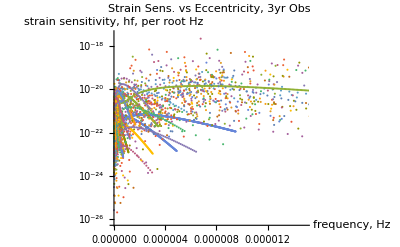

```mathematica
blogplot=ListLogPlot[strainSenseVfreq3yr, 
PlotLabel->"Strain Sens. vs Eccentricity, 3yr Obs",
AxesLabel->{"frequency, Hz", "strain sensitivity, hf, per root Hz"}]
```

```mathematica
fileString=myDir<>"hfVfreq"<>ToString[mylen]<>"exop3yr.png";
Export[fileString, blogplot, "PNG", ImageSize->{11,8.5}*72]
```

/home/gabella/Documents/astro/exop/hfVfreq766exop3yr.png

```mathematica
strainSenseVfreq10yr = Table[
Table[
{atab[[ii,2,kk, 1]], atab[[ii,2,kk, 2]]*rootNfcn[fdata6[[ii,cols["pl_orbper"]]]*secsDay, 10*secsYear, kk]*
√(10*secsYear) },{kk, 1, Length[ atab[[ii,2]] ]}
],
{ii, 1, Length[atab]}
];
strainSenseVfreq10yr[[1;;3]]//MatrixForm
```

({{5.99455×10^-9,4.57457×10^-22},{1.19891×10^-8,7.52022×10^-22},{1.79836×10^-8,1.22102×10^-21},{2.39782×10^-8,1.30361×10^-21},{2.99727×10^-8,1.19973×10^-21},{3.59673×10^-8,1.02267×10^-21},{4.19618×10^-8,8.31835×10^-22},{4.79564×10^-8,6.55553×10^-22},{5.39509×10^-8,5.04994×10^-22},{5.99455×10^-8,3.82384×10^-22},{6.594×10^-8,2.8568×10^-22},{7.19345×10^-8,2.11142×10^-22},{7.79291×10^-8,1.54678×10^-22},{8.39236×10^-8,1.12478×10^-22},{8.99182×10^-8,8.12804×10^-23}}
{{5.37385×10^-9,1.90609×10^-21},{1.07477×10^-8,1.47624×10^-21},{1.61216×10^-8,3.3804×10^-21},{2.14954×10^-8,4.42638×10^-21},{2.68693×10^-8,4.86088×10^-21},{3.22431×10^-8,4.89561×10^-21},{3.7617×10^-8,4.68304×10^-21},{4.29908×10^-8,4.32918×10^-21},{4.83647×10^-8,3.90584×10^-21},{5.37385×10^-8,3.46031×10^-21},{5.91124×10^-8,3.02258×10^-21},{6.44862×10^-8,2.61057×10^-21},{6.98601×10^-8,2.23402×10^-21},{7.52339×10^-8,1.89716×10^-21},{8.06078×10^-8,1.60066×10^-21},{8.59816×10^-8,1.34301×10^-21},{9.13555×10^-8,1.12142×10^-21},{9.67293×10^-8,9.3246×10^-22},{1.02103×10^-7,7.72463×10^-22},{1.07477×10^-7,6.37811×10^-22},{1.12851×10^-7,5.25079×10^-22},{1.18225×10^-7,4.31126×10^-22},{1.23599×10^-7,3.53136×10^-22}}
{{3.50151×10^-8,9.88422×10^-23},{7.00302×10^-8,3.74647×10^-22},{1.05045×10^-7,3.81894×10^-22},{1.4006×10^-7,2.78406×10^-22},{1.75075×10^-7,1.78163×10^-22},{2.1009×10^-7,1.0633×10^-22},{2.45106×10^-7,6.07565×10^-23}})

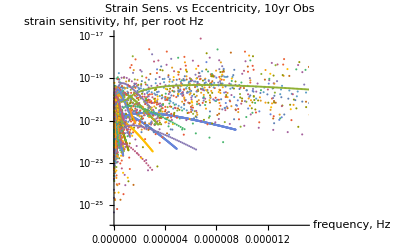

```mathematica
clogplot=ListLogPlot[strainSenseVfreq10yr, 
PlotLabel->"Strain Sens. vs Eccentricity, 10yr Obs",
AxesLabel->{"frequency, Hz", "strain sensitivity, hf, per root Hz"},
BaseStyle->{FontFamily->"Helvetica"}]
```

```mathematica
fileString = myDir<>"hfVfreq"<>ToString[mylen]<>"exop10yr.png";
Export[fileString, clogplot, "PNG", FontSize->4,ImageSize->{11,8.5}*72]
```

/home/gabella/Documents/astro/exop/hfVfreq766exop10yr.png

For xmgrace log plot need to drop the 0 strains, which come from the circular orbits for n=1 and 3, only n=2 is non-zero.

```mathematica
Flatten[ strainSenseVfreq10yr[[12;;14]],1 ]
```

{{3.52638×10^-6,2.77742×10^-21},{7.05275×10^-6,2.62796×10^-20},{0.0000105791,1.30957×10^-20},{1.01668×10^-8,5.14987×10^-22},{2.03336×10^-8,4.31585×10^-21},{3.05005×10^-8,2.39267×10^-21},{1.63654×10^-8,1.27786×10^-21},{3.27308×10^-8,4.0314×10^-21},{4.90962×10^-8,4.61433×10^-21},{6.54616×10^-8,3.72935×10^-21},{8.1827×10^-8,2.63812×10^-21},{9.81924×10^-8,1.73847×10^-21},{1.14558×10^-7,1.09622×10^-21},{1.30923×10^-7,6.70769×10^-22}}

```mathematica
aflat = Flatten[ strainSenseVfreq10yr, 1];
Print["Length of aflat is "<>ToString[ Length[aflat] ]<>"."]
aflatFiltered = {};
For[ii=1, ii≤Length[aflat], ii++, 
If[aflat[[ii,2]]==0, , AppendTo[aflatFiltered, aflat[[ii]] ] ];
];
Print["Length of aflatFiltered  is "<>ToString[ Length[aflatFiltered ] ]<>"."]
```

Length of aflat is 5725.

Length of aflatFiltered  is 5463.

```mathematica
Export[myDir<>"tenYearsEccen.dat",aflatFiltered ]
```

/home/gabella/Documents/astro/exop/tenYearsEccen.dat

## Frequency Bin and histogram to see the numbers of modes in the bin. Useful frequency range for LISA seems to be 1e-4 to 1 Hz, though we should use 1e-5 to 1 Hz, or even 1e-6 to 1 Hz.

```mathematica
strainSenseVfreq10yr[[3]]//MatrixForm  (* Each "row" is a planet at some eccentricity.  Then follows the Freq(Hz), Strain Sensitivity 10yr(per root Hz). *)
```

(3.50151×10^-8 | 9.88422×10^-23
7.00302×10^-8 | 3.74647×10^-22
1.05045×10^-7 | 3.81894×10^-22
1.4006×10^-7 | 2.78406×10^-22
1.75075×10^-7 | 1.78163×10^-22
2.1009×10^-7 | 1.0633×10^-22
2.45106×10^-7 | 6.07565×10^-23)

```mathematica
Length[strainSenseVfreq10yr]
```

766

```mathematica
Length[aflat]
```

5725

```mathematica
{aflat[[1;;4]]}//MatrixForm
```

((5.99455×10^-9
4.57457×10^-22) | (1.19891×10^-8
7.52022×10^-22) | (1.79836×10^-8
1.22102×10^-21) | (2.39782×10^-8
1.30361×10^-21))

```mathematica
{freqs, hfs}=Transpose[aflat];
```

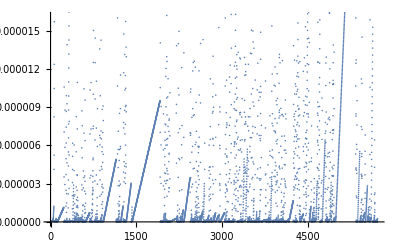

```mathematica
ListPlot[freqs]
```

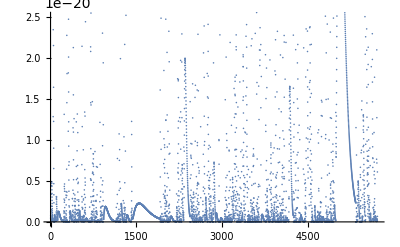

```mathematica
ListPlot[hfs]
```

Make a histogram out of the frequencies and see about logarithmic or not, what bin width for several modes in the bin.  Ignore below 1e-6 Hz, typically LISA folks go to 1e-4 and now with LPF success 1e-5 should be considered.

```mathematica
Length[freqs]
```

5725

```mathematica
{Min[freqs], Max[freqs]}
```

{5.76511×10^-11,0.000385675}

```mathematica
freqs[[1;;10]]
```

{5.99455×10^-9,1.19891×10^-8,1.79836×10^-8,2.39782×10^-8,2.99727×10^-8,3.59673×10^-8,4.19618×10^-8,4.79564×10^-8,5.39509×10^-8,5.99455×10^-8}

```mathematica
freqsSort = Sort[freqs, #1<#2&]; (* Usual sort, smallest to largest, ascending *)
```

```mathematica
(*{freqs, hfs}=Transpose[aflat];*)
aflatSort = Sort[aflat, #1[[1]]<#2[[1]] & ];
```

```mathematica
aflatSort[[1;;10]]
```

{{5.76511×10^-11,4.6875×10^-24},{1.15302×10^-10,1.8599×10^-23},{1.72953×10^-10,1.8392×10^-23},{2.30604×10^-10,1.30432×10^-23},{2.88255×10^-10,8.12493×10^-24},{3.45906×10^-10,4.72132×10^-24},{8.14889×10^-10,2.5761×10^-23},{1.32224×10^-9,7.43492×10^-23},{1.62978×10^-9,2.78123×10^-22},{1.84076×10^-9,1.66576×10^-23}}

```mathematica
freqsSort[[1;;10]]
```

{5.76511×10^-11,1.15302×10^-10,1.72953×10^-10,2.30604×10^-10,2.88255×10^-10,3.45906×10^-10,8.14889×10^-10,1.32224×10^-9,1.62978×10^-9,1.84076×10^-9}

```mathematica
Length[aflatSort]
```

5725

```mathematica
Clear[saveBigData]  (* For a pair of data {{freq1,hfs1}, {freq2,hfs2}...} *)
saveBigData[alist_] := Module[{aa={},bb, alim=10^-6},
For[i=1, i<=Length[alist], i++,
If[alist[[i]][[1]]≥alim, AppendTo[aa,alist[[i]]], ];
];
aa
]
```

```mathematica
aflatBig=saveBigData[aflatSort];
```

```mathematica
{aflatFreq,aflatHfs}=Transpose[aflatBig];{Length[aflatBig], Length[aflatFreq],Min[aflatFreq], Max[aflatFreq], Length[aflatHfs], Min[aflatHfs], Max[aflatHfs]}
```

{2516,2516,1.00259×10^-6,0.000385675,2516,0.,1.11645×10^-17}

```mathematica
Clear[saveBig]
saveBig[alist_] := Module[{aa={},bb, alim=10^-6},
For[i=1, i<=Length[alist], i++,
If[alist[[i]]≥alim, AppendTo[aa,alist[[i]]], ];
];
aa
]
```

```mathematica
freqsBig=saveBig[freqsSort];
```

```mathematica
{Length[freqsBig], Min[freqsBig], Max[freqsBig]}
```

{2516,1.00259×10^-6,0.000385675}

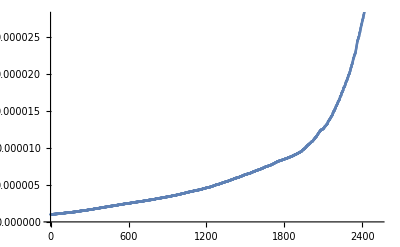

```mathematica
ListPlot[freqsBig]
```

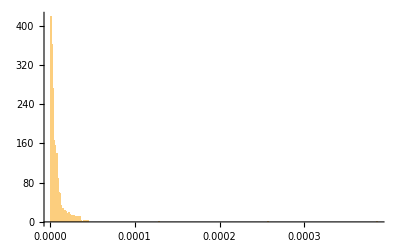

```mathematica
Histogram[freqsBig, PlotRange->All]
```

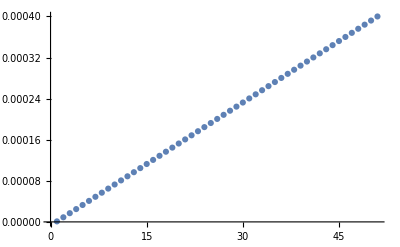

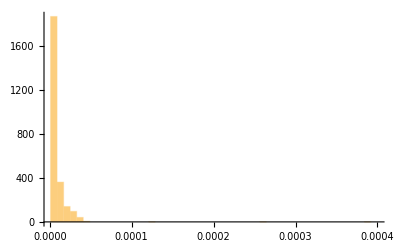

```mathematica
amin=10^-6;
amax=4 10^-4;
myBins={Table[amin+(amax-amin)*i/50,{i,0,50}]};
ListPlot[myBins]
Histogram[freqsBig,myBins, PlotRange->All]
```

What is the bins if I want about 10 points per bin?  Is that fair to change the binning to do that?  Kelly says that usually astrophysics likes even bins in the Log space.

Binsize 0.0260206 No. bin boundaries 101

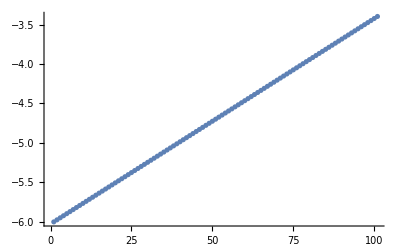

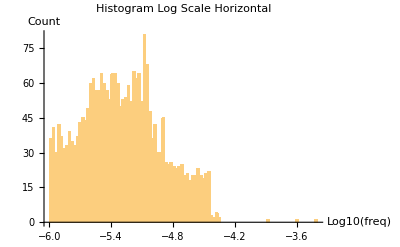

```mathematica
amin=Log10[1. 10^-6];
amax=Log10[4. 10^-4];
nBins = 100;
myBins={Table[amin+(amax-amin)*i/nBins,{i,0,nBins}]};
Print["Binsize ",(amax-amin)/nBins//N, " No. bin boundaries ", Length[myBins[[1]] ] ]
ListPlot[myBins]
Histogram[Log10[freqsBig],myBins, PlotRange->All,
PlotLabel->"Histogram Log Scale Horizontal",
AxesLabel->{"Log10(freq)","Count"}]
(*Histogram[ Log10[freqsBig]]*)
```

```mathematica
Print["Binsize dLog  ",aa=(amax-amin)/nBins//N, "  10^amin  ", 10^amin//N,"  multiple 10^dLog  ", 10^aa]
```

Binsize dLog  0.0260206  10^amin  1.×10^-6  multiple 10^dLog  1.06175

Binsize 0.130103 No. bin boundaries 21

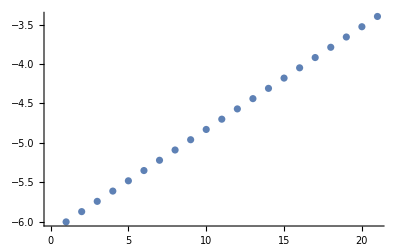

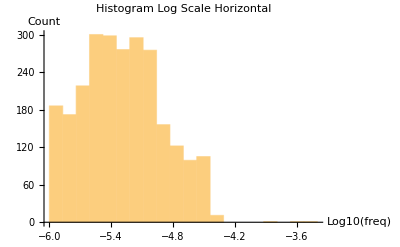

Binsize dLog  0.130103  10^amin  1.×10^-6  multiple 10^dLog  1.34928

```mathematica
amin=Log10[1. 10^-6];
amax=Log10[4. 10^-4];
nBins = 20;
myBins={Table[amin+(amax-amin)*i/nBins,{i,0,nBins}]};
Print["Binsize ",(amax-amin)/nBins//N, " No. bin boundaries ", Length[myBins[[1]] ] ]
ListPlot[myBins]
Histogram[Log10[freqsBig],myBins, PlotRange->All,
PlotLabel->"Histogram Log Scale Horizontal",
AxesLabel->{"Log10(freq)","Count"}]
(*Histogram[ Log10[freqsBig]]*)
Print["Binsize dLog  ",aa=(amax-amin)/nBins//N, "  10^amin  ", 10^amin//N,"  multiple 10^dLog  ", 10^aa]
```

```mathematica
myBins
(10^#&) /@ myBins
```

{{-6.,-5.8699,-5.73979,-5.60969,-5.47959,-5.34949,-5.21938,-5.08928,-4.95918,-4.82907,-4.69897,-4.56887,-4.43876,-4.30866,-4.17856,-4.04846,-3.91835,-3.78825,-3.65815,-3.52804,-3.39794}}

{{1.×10^-6,1.34928×10^-6,1.82056×10^-6,2.45646×10^-6,3.31445×10^-6,4.47214×10^-6,6.03418×10^-6,8.14181×10^-6,0.0000109856,0.0000148227,0.00002,0.0000269857,0.0000364113,0.0000491291,0.0000662891,0.0000894427,0.000120684,0.000162836,0.000219712,0.000296454,0.0004}}

Find those frequencies in the bin for RMS addition.

```mathematica
Clear[inBin]
inBin[alist_,lower_,upper_] := Module[{aa={}},
For[i=1, i<=Length[alist], i++,
If[alist[[i]]≥lower && alist[[i]]<upper, AppendTo[aa,alist[[i]]], ];
];
aa
]
```

```mathematica
myBins[[1]]
```

{-6.,-5.8699,-5.73979,-5.60969,-5.47959,-5.34949,-5.21938,-5.08928,-4.95918,-4.82907,-4.69897,-4.56887,-4.43876,-4.30866,-4.17856,-4.04846,-3.91835,-3.78825,-3.65815,-3.52804,-3.39794}

```mathematica
Length[myBins[[1]]]
```

21

```mathematica
putInBins = Table[
{aa=inBin[ Log10[freqsBig],myBins[[1]][[ii]],myBins[[1]][[ii+1]]  ],Length[aa]}, {ii,1,Length[myBins[[1]]]-1}
];
```

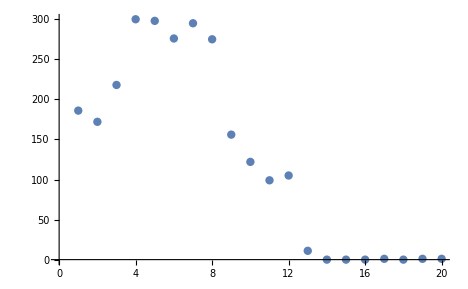

```mathematica
{freqListBin,countBin}=Transpose[putInBins];
ListPlot[countBin]
```

```mathematica
freqListBin[[1;;2]] (* From Exop data, modes in the first bin, second, etc. *)
```

{{-5.99888,-5.9984,-5.99628,-5.99616,-5.99554,-5.99448,-5.99321,-5.99234,-5.99229,-5.99187,-5.99098,-5.98954,-5.9886,-5.98798,-5.98789,-5.98751,-5.98674,-5.9862,-5.98543,-5.98438,-5.98382,-5.98318,-5.98311,-5.98162,-5.98039,-5.97984,-5.97977,-5.97924,-5.97891,-5.97853,-5.97732,-5.97718,-5.97706,-5.97626,-5.97529,-5.97467,-5.97338,-5.97284,-5.97252,-5.97215,-5.9718,-5.97144,-5.97085,-5.97047,-5.96946,-5.9681,-5.96632,-5.96602,-5.96575,-5.96533,-5.96398,-5.96266,-5.96254,-5.9622,-5.96202,-5.9617,-5.96061,-5.96042,-5.95992,-5.95933,-5.95885,-5.95812,-5.95671,-5.95629,-5.95408,-5.95406,-5.95325,-5.95313,-5.95106,-5.95073,-5.95008,-5.94979,-5.94977,-5.94962,-5.94874,-5.94871,-5.94823,-5.94783,-5.94761,-5.94639,-5.94633,-5.94611,-5.94563,-5.94242,-5.94229,-5.94171,-5.94131,-5.94053,-5.93736,-5.93713,-5.93639,-5.93603,-5.93559,-5.93487,-5.93475,-5.93402,-5.93402,-5.93099,-5.93057,-5.92924,-5.92684,-5.9259,-5.92585,-5.92394,-5.92378,-5.92369,-5.92363,-5.92192,-5.9219,-5.92127,-5.92038,-5.91978,-5.91969,-5.91793,-5.91787,-5.91485,-5.91418,-5.91345,-5.91283,-5.91211,-5.91203,-5.91147,-5.91118,-5.91035,-5.91023,-5.91011,-5.90953,-5.90946,-5.90931,-5.90835,-5.90794,-5.90754,-5.90693,-5.90599,-5.90576,-5.90441,-5.90413,-5.90392,-5.90255,-5.90242,-5.90238,-5.90166,-5.90083,-5.89925,-5.89821,-5.89814,-5.89794,-5.89708,-5.89611,-5.89487,-5.89486,-5.89322,-5.89262,-5.89171,-5.89159,-5.89078,-5.88983,-5.88746,-5.88745,-5.8863,-5.88628,-5.88609,-5.88518,-5.88476,-5.88429,-5.88348,-5.88293,-5.88233,-5.88015,-5.8797,-5.87966,-5.87911,-5.87838,-5.87753,-5.87752,-5.8763,-5.87591,-5.87401,-5.87394,-5.8736,-5.87336,-5.87332,-5.87297,-5.87248,-5.87187,-5.8703},{-5.86924,-5.86916,-5.86865,-5.86865,-5.86806,-5.86723,-5.86707,-5.86591,-5.86231,-5.86229,-5.86134,-5.86091,-5.86031,-5.85896,-5.85843,-5.8579,-5.85545,-5.85497,-5.85483,-5.85212,-5.85132,-5.85036,-5.84908,-5.84884,-5.84872,-5.84844,-5.84822,-5.84754,-5.84606,-5.84558,-5.84538,-5.84496,-5.84294,-5.84209,-5.8406,-5.83875,-5.83868,-5.83711,-5.83698,-5.83556,-5.8349,-5.8348,-5.83325,-5.83254,-5.83222,-5.83135,-5.83119,-5.83013,-5.82943,-5.82914,-5.82912,-5.82831,-5.82698,-5.82672,-5.82652,-5.82579,-5.82568,-5.82403,-5.82278,-5.82031,-5.82007,-5.81991,-5.8198,-5.81945,-5.81839,-5.81712,-5.81654,-5.8162,-5.81512,-5.81456,-5.81454,-5.8132,-5.81065,-5.81058,-5.81055,-5.81038,-5.80993,-5.80908,-5.80704,-5.80701,-5.80605,-5.80523,-5.80493,-5.8043,-5.80375,-5.80368,-5.80348,-5.80315,-5.80244,-5.80189,-5.8017,-5.80097,-5.80017,-5.7992,-5.79835,-5.79831,-5.79698,-5.79497,-5.79497,-5.79476,-5.79463,-5.79309,-5.79292,-5.7924,-5.79062,-5.78907,-5.78859,-5.78789,-5.78657,-5.78645,-5.78561,-5.78533,-5.78432,-5.78324,-5.78275,-5.78128,-5.78082,-5.77899,-5.77767,-5.77748,-5.77716,-5.77704,-5.77598,-5.77589,-5.77572,-5.77514,-5.77494,-5.77341,-5.77332,-5.7732,-5.77316,-5.77265,-5.77252,-5.77214,-5.76954,-5.76816,-5.76768,-5.76767,-5.76762,-5.76571,-5.76401,-5.76318,-5.76278,-5.76049,-5.75999,-5.75994,-5.7595,-5.75854,-5.75792,-5.75748,-5.75441,-5.75345,-5.75315,-5.75313,-5.75266,-5.75259,-5.75153,-5.75087,-5.74892,-5.74843,-5.74838,-5.74782,-5.74769,-5.74754,-5.74694,-5.74583,-5.74581,-5.74492,-5.74371,-5.74368,-5.74299,-5.74256}}

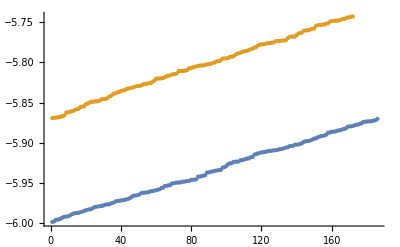

```mathematica
ListPlot[{freqListBin[[1]], freqListBin[[2]]}, PlotRange->All]
```

```mathematica
freqsBig[[1;;14]]
```

{1.00259×10^-6,1.00369×10^-6,1.0086×10^-6,1.00887×10^-6,1.01032×10^-6,1.01279×10^-6,1.01576×10^-6,1.01779×10^-6,1.01791×10^-6,1.01889×10^-6,1.02098×10^-6,1.02439×10^-6,1.0266×10^-6,1.02807×10^-6}

```mathematica
{1/freqsBig[[1]], freqsBig[[1]], Log10[freqsBig[[1]]], Floor[  Log10[freqsBig[[1]]] ] }
```

{997415.,1.00259×10^-6,-5.99888,-6}

```mathematica
(* Put the bin boundary at the harmonic average of the two points across the boundary. *)
(*findBins[alist_,num_]:=Module[{asort, aa,bb,cc, abins={}},
asort = Sort[alist];
aa=asort[[1]];  (* first point, but bin at next integer down in the mantissa. *)
bb= 10^Floor[  Log10[ aa[[1]]] ]; (* Smallest first, use Log10 and 10 to the power. *)
AppendTo[abins, bb];

bb = Quotient[Length[asort],10]; (* The integer division of the two. *)
aa = Mod[Length[asort],10];  (* The remainder of the division of the two. *)
If[bb==0,
{AppendTo[abins, 10^Ceiling[ Log10[ asort[[-1]] ] ] ],abins},
For[i=1, i≤bb, i++,
AppendTo[abins, Sqrt[ asort[[i*10]]*asort[[i*10+1]] ] ];
],
 ]
*)
```

Exop data from above.
{freqs, hfs}=Transpose[aflat];
Also aflatSort, ordered by frequency,and aflatBig, ordered by frequency and with frequency larger than 1e-6 Hz.

Insert some fake data at 2e-4 Hz and hfs {1,2,3,4,5}e-18 per root hz.  f=2e-4 Hz has not data in that bin!

```mathematica
aflatBig[[1;;4]]
```

{{1.00259×10^-6,1.82183×10^-21},{1.00369×10^-6,3.96365×10^-22},{1.0086×10^-6,7.13985×10^-23},{1.00887×10^-6,1.5802×10^-21}}

```mathematica
fakeData = {{2. 10^-4,1. 10^-18},{2. 10^-4,2. 10^-18},{2. 10^-4,3. 10^-18},{2. 10^-4,4. 10^-18},{2. 10^-4,5. 10^-18}};
```

```mathematica
If[False,{Length[aflatBig],
aflatBig=aflatBig~Join~fakeData;
Length[aflatBig]}, ] (* Join the fake data to the actual.  Keep this Off most of the time. *)
```

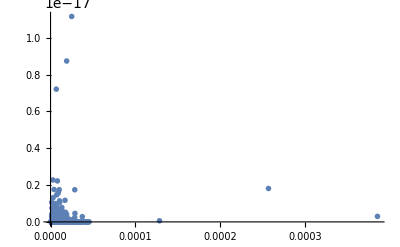

```mathematica
aplot=ListPlot[aflatBig, PlotStyle->{PointSize[0.01]},PlotRange->All]
```

```mathematica
myBins[[1]]
```

{-6.,-5.8699,-5.73979,-5.60969,-5.47959,-5.34949,-5.21938,-5.08928,-4.95918,-4.82907,-4.69897,-4.56887,-4.43876,-4.30866,-4.17856,-4.04846,-3.91835,-3.78825,-3.65815,-3.52804,-3.39794}

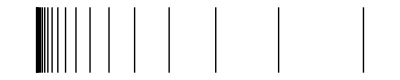

```mathematica
bplot=Show[Graphics[Table[
Line[{{10^(myBins[[1]][[i]]),0.5 10^-18},{10^(myBins[[1]][[i]]),10 10^-18}}],{i,1, Length[myBins[[1]] ]}
]
]
]
```

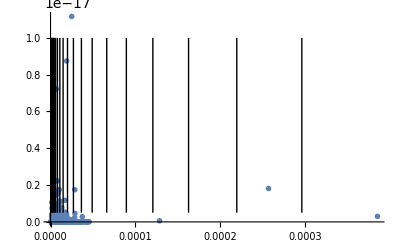

```mathematica
Show[{aplot,bplot}]
```

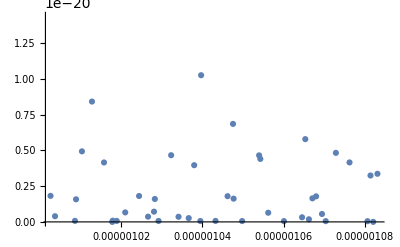

```mathematica
ListPlot[aflatBig[[1;;50]] ](* first 50 points *)
```

```mathematica
myBins
```

{{-6.,-5.8699,-5.73979,-5.60969,-5.47959,-5.34949,-5.21938,-5.08928,-4.95918,-4.82907,-4.69897,-4.56887,-4.43876,-4.30866,-4.17856,-4.04846,-3.91835,-3.78825,-3.65815,-3.52804,-3.39794}}

Bin the aflatBig.  2D version of BinLists looks like the right way to go.  The second dimension is {{-Infinity,Infinity}} for the binning, this also adds an extra set of parentheses.

```mathematica
(* use myBins, in the log-space of freqency from 1e-6 to 4e-4 Hz *)

pairsInBin={};
{freqBig, hfsBig}=Transpose[aflatBig];
aflatBigLogFreq = Transpose[ {Log10[freqBig],hfsBig}];
aflatBL=BinLists[aflatBigLogFreq,myBins,{{-∞,+∞}}];
```

```mathematica
{aflatBigLogFreq[[-7;;-1]],hfsBig[[-7;;-1]]}
```

{{{-4.36792,0.},{-4.36435,2.53499×10^-21},{-4.34653,5.66429×10^-22},{-4.34274,1.31726×10^-21},{-3.8909,6.03194×10^-20},{-3.58987,1.81605×10^-18},{-3.41378,3.00403×10^-19}},{0.,2.53499×10^-21,5.66429×10^-22,1.31726×10^-21,6.03194×10^-20,1.81605×10^-18,3.00403×10^-19}}

```mathematica
10^-1.6987
```

0.0200124

```mathematica
aflatBL[[-3;;-1]]
```

{{{}},{{{-3.58987,1.81605×10^-18}}},{{{-3.41378,3.00403×10^-19}}}}

```mathematica
{Length[aflatBig], Length[myBins],Length[aflatBL], Length[aflatBL[[1,1]]],Length[aflatBL[[2,1]]]}
aflatBL[[-1,1]]
(*Transpose[  aflatBL[[8,1]]  ]
aflatBL[[8,1]]*)
```

{2516,1,20,186,172}

{{-3.41378,3.00403×10^-19}}

```mathematica
(* Check the count, all elements of the bin lists should equal the original vector length. *)
(* Woo Hoo! Length[aflatBig] == sum of the lengths of the binned vector! *)
```

```mathematica
Sum[Length[aflatBL[[i,1]] ],{i,1,Length[aflatBL]}]
```

2516

```mathematica
{Length[myBins], Length[myBins[[1]]], (myBins[[1,2]]-myBins[[1,1]]),(myBins[[1,3]]-myBins[[1,2]]), 10^ (myBins[[1,3]]-myBins[[1,2]])}
```

{1,21,0.130103,0.130103,1.34928}

```mathematica
Clear[addLikeRMS];
addLikeRMS[a_]:=Sqrt[ Sum[a[[i]]^2,{i,1,Length[a]} ] ]
```

```mathematica
??addLikeRMS
```

Global`addLikeRMS

addLikeRMS[a_]:=√(∑_(i=1)^Length[a] a⟦i⟧^2)

```mathematica
{ addLikeRMS[{1. 10^-18,2. 10^-18,3. 10^-18,4. 10^-18,5. 10^-18}], Sqrt[ 1*1+2*2+3*3+4*4+5*5 ]//N}
```

{7.4162×10^-18,7.4162}

```mathematica
(* Add up within the bin the hfs like RMS. Use the CENTROID of the log-space frequency??!!   *)
logfreq={};
hfsrms={};
cntLogfreq={};
cntHfsrms = {};
For[i=1,i≤Length[aflatBL],i++,
If[ Length[ aflatBL[[i,1]] ]≠0,
Module[{alogFreq={},aHfs={} },
(*Print["  i is ",i];*)
{alogFreq, aHfs}=Transpose[ aflatBL[[i,1]] ];
logfreq~AppendTo~( Mean[ alogFreq ] ); (*( (myBins[[1,i]]+myBins[[1,i+1]])/2 );*)
If[i==12,Print["aHfs and addLikeRMS\n",aHfs, "\n",addLikeRMS[aHfs] ];, ];
hfsrms~AppendTo~addLikeRMS[ aHfs ]; 
cntLogfreq~AppendTo~Length[alogFreq];
cntHfsrms~AppendTo~Length[ aHfs ];
],
{
(*Print["*** Zero length aflatBL, i is ",i];*)
logfreq~AppendTo~( Mean[ {myBins[[1,i]], myBins[[1,i+1]]} ] );
hfsrms~AppendTo~( 0.0 );
cntLogfreq~AppendTo~(0);
cntHfsrms~AppendTo~(0);
}
]
]
```

aHfs and addLikeRMS
{7.76997×10^-21,7.67077×10^-21,7.57273×10^-21,0.,1.17583×10^-20,7.47582×10^-21,7.38004×10^-21,3.17122×10^-21,7.28538×10^-21,7.19183×10^-21,7.09937×10^-21,7.008×10^-21,7.12322×10^-21,6.9177×10^-21,6.82846×10^-21,6.74028×10^-21,6.65314×10^-21,6.56704×10^-21,6.48196×10^-21,2.38529×10^-19,1.74778×10^-18,0.,6.39789×10^-21,6.31482×10^-21,4.77514×10^-20,6.23275×10^-21,4.59958×10^-19,6.15165×10^-21,6.07154×10^-21,5.99238×10^-21,5.91418×10^-21,5.83691×10^-21,5.76059×10^-21,5.68518×10^-21,5.61069×10^-21,5.53711×10^-21,5.46442×10^-21,5.39261×10^-21,2.53204×10^-21,5.32168×10^-21,5.25162×10^-21,5.18242×10^-21,5.11406×10^-21,5.04655×10^-21,4.97986×10^-21,4.914×10^-21,4.84895×10^-21,4.7847×10^-21,4.72125×10^-21,4.65859×10^-21,4.5967×10^-21,4.53558×10^-21,4.47522×10^-21,5.22486×10^-21,4.41562×10^-21,4.35676×10^-21,4.29864×10^-21,4.24124×10^-21,4.18456×10^-21,4.1286×10^-21,4.07334×10^-21,4.01877×10^-21,3.96489×10^-21,3.91169×10^-21,2.00358×10^-21,3.85917×10^-21,3.80731×10^-21,3.7561×10^-21,3.70555×10^-21,3.65564×10^-21,3.60636×10^-21,3.55771×10^-21,3.50968×10^-21,3.46226×10^-21,3.41545×10^-21,3.36924×10^-21,3.32362×10^-21,3.27859×10^-21,3.23413×10^-21,3.19025×10^-21,3.14693×10^-21,0.,3.10417×10^-21,3.06196×10^-21,3.02029×10^-21,2.97916×10^-21,2.93857×10^-21,2.8985×10^-21,2.85895×10^-21,2.81992×10^-21,3.76778×10^-21,1.57356×10^-21,2.78139×10^-21,2.74336×10^-21,2.70583×10^-21,2.66879×10^-21,2.63223×10^-21,2.59615×10^-21,2.56054×10^-21,2.5254×10^-21,2.49071×10^-21,2.45649×10^-21,2.42271×10^-21,2.38937×10^-21,2.35648×10^-21}
1.82423×10^-18

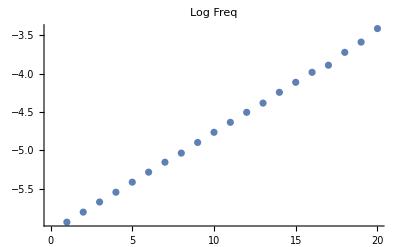

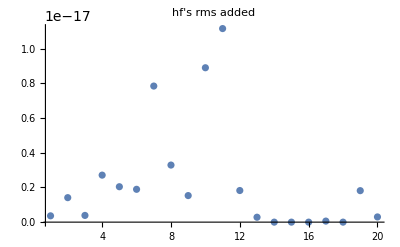

```mathematica
ListPlot[logfreq, PlotLabel->"Log Freq"]
ListPlot[hfsrms, PlotLabel->"hf's rms added", PlotRange->All]
```

Convert into data like the other hf’s in the Grace plots...just pairs of freq and hfs to export.

```mathematica
rmsHfData=Transpose[  {10^logfreq, hfsrms} ];
```

```mathematica
rmsHfData
```

{{1.16366×10^-6,3.63667×10^-19},{1.57127×10^-6,1.4127×10^-18},{2.12766×10^-6,3.8744×10^-19},{2.85249×10^-6,2.71196×10^-18},{3.85608×10^-6,2.04319×10^-18},{5.20589×10^-6,1.89415×10^-18},{7.01321×10^-6,7.85142×10^-18},{9.22292×10^-6,3.29298×10^-18},{0.0000126806,1.53222×10^-18},{0.0000172047,8.90785×10^-18},{0.0000231928,1.11683×10^-17},{0.000031312,1.82423×10^-18},{0.000041303,2.83088×10^-19},{0.0000570677,0.},{0.0000770005,0.},{0.000103895,0.},{0.000128558,6.03194×10^-20},{0.000189148,0.},{0.000257116,1.81605×10^-18},{0.000385675,3.00403×10^-19}}

```mathematica
{{"Freq","hfs RMS sum"}}~Join~rmsHfData//TableForm
```

Freq | hfs RMS sum
1.16366×10^-6 | 3.63667×10^-19
1.57127×10^-6 | 1.4127×10^-18
2.12766×10^-6 | 3.8744×10^-19
2.85249×10^-6 | 2.71196×10^-18
3.85608×10^-6 | 2.04319×10^-18
5.20589×10^-6 | 1.89415×10^-18
7.01321×10^-6 | 7.85142×10^-18
9.22292×10^-6 | 3.29298×10^-18
0.0000126806 | 1.53222×10^-18
0.0000172047 | 8.90785×10^-18
0.0000231928 | 1.11683×10^-17
0.000031312 | 1.82423×10^-18
0.000041303 | 2.83088×10^-19
0.0000570677 | 0.
0.0000770005 | 0.
0.000103895 | 0.
0.000128558 | 6.03194×10^-20
0.000189148 | 0.
0.000257116 | 1.81605×10^-18
0.000385675 | 3.00403×10^-19

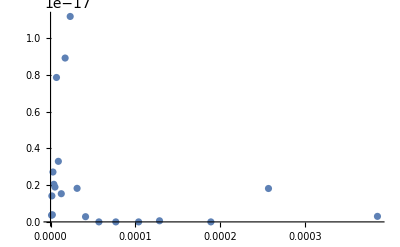

```mathematica
ListPlot[rmsHfData]
```

```mathematica
Export[myDir<>"hfsRMS20bins.dat",rmsHfData ]
```

/home/gabella/Documents/astro/exop/hfsRMS20bins.dat

Put in some fake data to check the RMS addition.  At 2e-2 Hz and at values 1,2,3,4,5 e -18 per root Hz.

## Possible LISA bandwidths for root-mean-squaring of the GW modes in freq space.

one year, three year, one day, one hour

```mathematica
{1/secsYear, 1/(3.*secsYear), 1/(24.*3600.),1/(3600.), Sqrt[secsYear], 1/Sqrt[secsYear]}
```

{3.1689×10^-8,1.0563×10^-8,0.0000115741,0.000277778,5617.54,0.000178014}

LISA Arm lengths and the ripples on the right of the sensitivity curve.  TOF?

```mathematica
Clear[tof];
tof[arm_,n_]:= n*2*arm/cee
```

```mathematica
{{"n","time, 5e9", "freq, 1e9", "time, 5e9", "freq, 1e9"}}~Join~Table[{n, aa=tof[5 10^9,n],1/aa, bb=tof[1 10^9,n], 1/bb},{n,1,5}]//TableForm
```

n | time, 5e9 | freq, 1e9 | time, 5e9 | freq, 1e9
1 | 33.3564 | 0.0299792 | 6.67128 | 0.149896
2 | 66.7128 | 0.0149896 | 13.3426 | 0.0749481
3 | 100.069 | 0.00999308 | 20.0138 | 0.0499654
4 | 133.426 | 0.00749481 | 26.6851 | 0.0374741
5 | 166.782 | 0.00599585 | 33.3564 | 0.0299792

Tinto et al. 2002, page 38,  say BW 1cycle per year or 3.17e-8 Hz (?).

## Bar Charts

```mathematica
p=Table[{n^1.3,Prime[n]},{n,10}]
```

{{1.,2},{2.46229,3},{4.17117,5},{6.06287,7},{8.10328,11},{10.2706,13},{12.5495,17},{14.9285,19},{17.3986,23},{19.9526,29}}

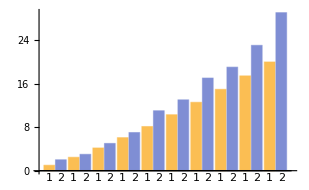

```mathematica
BarChart[p, ChartLabels->Range[10]]
```

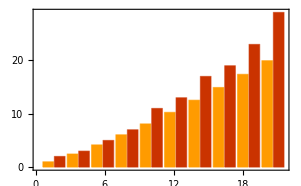

```mathematica
BarChart[p,PlotTheme->"Web"]
```

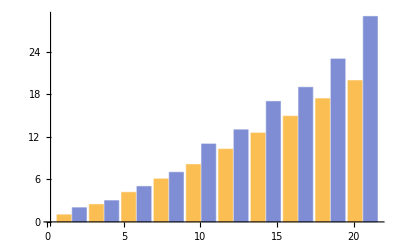

```mathematica
Show[ BarChart[p, Axes->None],Axes->True, Ticks->Automatic] (* Weird! *)
```

## Perihelion Shift

From MTW page 1110, the shift per orbit in radians!  Exop work the a is harder than the period.  Use Kepler, Pb^2=G M_tot/a^3.

```mathematica
dϕ = (6 π G M/c^2)/(a (1-e^2))
```

(6 G M π)/(a c^2 (1-e^2))

```mathematica
Subscript[ωdot, MTW] = 3/(c^2(1-e^2)) (G M)^(3/2)/a^(5/2) (* in terms of a, M is mtot, papers like T or Subscript[P, b] the period *)
```

(3 (G M)^(3/2))/(a^(5/2) c^2 (1-e^2))

```mathematica
Subscript[ωdot, WT] = 3/(c^2(1-e^2)) (G M)^(2/3)/(Subscript[P, b]/ (2 π))^(5/3)(* This is NOW RIGHT!  Weisberg and Taylor 2010, eqn 1, note the difference with above and it shows up in 2 Subscript[πP, b] which is close to 2π/Subscript[P, b] which is natural for rad/s to secs period. Copying their paper 2005 they give 3/(c^2(1-e^2)) (G M)^(2/3)/(Subscript[P, b] 2 π)^(5/3) as the first formula which is wrong, the second formula with units put in seems right.  *)
```

(6 2^(2/3) (G M)^(2/3) π^(5/3))/(c^2 (1-e^2) P_b^(5/3))

For the Hulse-Taylor pulsar it is...

## Pulsars PSR J1913-16 (“Hulse-Taylor”), PSR J2222-0137A and B (“Double Pulsar”), and the Exoplanet PSR J1719-1438 (“Diamond planet”)

Hulse-Taylor PSR B1913+16, 2010 ApJ paper especially

```mathematica
mht1 = 1.4398;
mht2 = 1.387; (* msol, mass in solar masses *)
perht = 7.75194*60.0*60.0; (* s, period in seconds *)
eccht = 0.617; (* eccentricity *)
aht = 1.95 10^9; (* m,semi-major axis ... where does this come from ???  a sin i is 2.34 secs ?? *)
```

```mathematica
asemi = (bigG mtot per^2)^(1/3)
```

0.000405626 (mtot per^2)^(1/3)

```mathematica
tdotOvert = -96/5(bigG^(5/3)mred mtot^(2/3))/cee^5(per/(2π))^(-8/3)smaf[e]    (* Maggiore's Eqn 4.79 *)
```

-(1.17032×10^-56 (1+(73 e^2)/24+(37 e^4)/96) mred mtot^(2/3))/((1-e^2)^(7/2) per^(8/3))

```mathematica
pbDot = -(192π)/5(bigG^(5/3)mred mtot^(2/3))/cee^5(per/(2π))^(-5/3)smaf[e]  (* Maggiore's Eqn. 6.4, also Peters & Mathews? *)
```

-(1.17032×10^-56 (1+(73 e^2)/24+(37 e^4)/96) mred mtot^(2/3))/((1-e^2)^(7/2) per^(5/3))

```mathematica
{redM[mht1,mht2],totM[mht1,mht2]}
 mhtred=redM[mht1,mht2]*massSun(* kg *)
mhttot=totM[mht1,mht2]*massSun
aht = asemi/.{mtot->mhttot, per->perht}
```

{0.706453,2.8268}

1.40584×10^30

5.62533×10^30

6.63717×10^9

```mathematica
totM[mht1,mht2]^(2/3)*2.11  (* advance of the periastron in degs/year from Weisberg et al. 2010 *)
```

4.21838

```mathematica
{mhtred, mhttot, eccht, perht}
```

{1.40584×10^30,5.62533×10^30,0.617,27907.}

Relativistic Period slowing.  Published number is

```mathematica
relPeriodSlowing=tdotOvert *perht/. {mred->mhtred, mtot->mhttot, e->eccht, per->perht}
```

-2.40034×10^-12

```mathematica
relPeriodSlowingPerYear = relPeriodSlowing*secsYear  (* secs per secs *)
```

-0.0000757468

```mathematica
relSlowing = pbDot /. {mred->mhtred, mtot->mhttot, e->eccht, per->perht}
```

-2.40034×10^-12

```mathematica
relSlowingPerYear = relSlowing*secsYear
```

-0.0000757468

### Perihelion Shift, papers put it at 4.226595(5) deg/yr

```mathematica
Subscript[dϕ, HT] = dϕ/.{G->bigG, c->cee, a->aht, e->eccht,M->mhttot} (* Rads per orbit *)
Subscript[dϕ, HT]/perht*180./π*secsYear  (* degs per year *)
```

0.0000191554

1.24106

rads per sec, degs per year

```mathematica
{aht, (bigG mhttot perht^2)^(1/3)}
```

{6.63717×10^9,6.63717×10^9}

```mathematica
Subscript[dϕ, HT] = dϕ/.{G->bigG, c->cee, a->(bigG mhttot perht^2)^(1/3), e->eccht,M->mhttot} (* Rads per orbit *)
Subscript[dϕ, HT]*180./π*secsYear
```

0.0000191554

34634.3

```mathematica
aMTW=Subscript[ωdot, MTW] /. {G->bigG, c->cee, a->aht, e->eccht,M->mhttot} (* Rads per sec *)
aWT=Subscript[ωdot, WT] /. {G->bigG, c->cee, a->aht, e->eccht,M->mhttot} (* Rads per sec *)
```

1.09244×10^-10

0.0600095/P_b^(5/3)

```mathematica
{Subscript[ωdot, MTW], Subscript[ωdot, WT]}/. {G->bigG, c->cee, a->aht, e->eccht,M->mhttot, Subscript[P, b]->0.323*24*3600.}
```

{1.09244×10^-10,2.33718×10^-9}

degs per year

```mathematica
{aMTW, aWT}*secsYear*180/π
```

{0.197521,(1.08501×10^8)/P_b^(5/3)}

Check the Keplers Law connection semimajor axis and the period, maybe buggered in PSR 1913+16.
Hmm, seem to know P_b directly from the data but not the semi-major axis, only the a sin i, i is inclination.

```mathematica
check={Subscript[P, b],2π √(a^3/(G M)), a,( G M (Subscript[P, b]/(2π))^2)^(1/3)}
```

{P_b,2 √(a^3/(G M)) π,a,((G M P_b^2)^(1/3))/(2 π)^(2/3)}

```mathematica
check/.{G->bigG, M->mhttot,Subscript[P, b]->0.323*24*3600, a->57.91 10^9}
```

{27907.2,4.51906×10^6,5.791×10^10,1.94924×10^9}

For Mercury, M=Msun, e=0.2056  , a=57.91e9 m

```mathematica
Subscript[dϕ, Merc] = dϕ/.{G->bigG, c->cee, a->57.81 10^9, e->0.2056,M->1.99 10^30}
```

5.03087×10^-7

```mathematica
Subscript[dϕ, Merc]*secsYear*360.0/(2π)
```

909.615

## All Three Pulsars, one data set

Name, notes/nickname, mass1 (Msun), mass2 (Msun), period (days), semi-major axis (au), eccentricity, distance (pc) .
Refs, exoplanet database, Weisberg et al 2010, “Binary Radio Pulsars” Rasio and Stairs, eds, 2005 .

```mathematica
psrData = {{"PSR J1719-1438", "Diamond Planet", 1.4, 1.02*massJs, 0.09071, 0.0044, 0.06, 1200.0},
{"PSR J1913+16", "Hulse-Taylor", 1.44,1.389, 0.323, 0.0047, 0.617, 9900},
{"PSR J0737-3039AB", "Double Pulsar", 1.337, 1.250, 0.10225, 0.00283,0.0878,600}};  
{{"name", "name2", "mass1(Msun)", "mass2(Msun)", "period(d)", "semimajor axis(au)","eccentricity", "distance(pc)"}}~Join~ psrData//TableForm
```

name | name2 | mass1(Msun) | mass2(Msun) | period(d) | semimajor axis(au) | eccentricity | distance(pc)
PSR J1719-1438 | Diamond Planet | 1.4 | 0.000973869 | 0.09071 | 0.0044 | 0.06 | 1200.
PSR J1913+16 | Hulse-Taylor | 1.44 | 1.389 | 0.323 | 0.0047 | 0.617 | 9900
PSR J0737-3039AB | Double Pulsar | 1.337 | 1.25 | 0.10225 | 0.00283 | 0.0878 | 600

```mathematica
psrCols = <||>;  (* Use an Association as an enum, or Dictionary *)
psrCols["name"]=1; psrCols["name2"]=2;
psrCols["mass1"]=3; psrCols["mass2"]=4; psrCols["period"]=5; psrCols["semimajor"]=6; psrCols["eccentricity"]=7; psrCols["distance"]=8;
```

```mathematica
psrData[[;;,psrCols["distance"]]]
```

{1200.,9900,600}

### Some calculations

Compare some Kepler relationships between Period and semi-major axis.  Seem not to be true in relativistic systems.  The measure a Sin[i], the inclination, it appears.  Pulsar people put that in units of seconds.

```mathematica
{{"Name","Period Sq", "a^3 *coeffs"}}~Join~Table[
{psrData[[i,psrCols["name"] ]], (psrData[[i,psrCols["period"] ]]*secsDay)^2, (psrData[[i,psrCols["semimajor"] ]]*au)^3((2π)^2/(bigG (psrData[[i,psrCols["mass1"] ]]+psrData[[i,psrCols["mass2"] ]])*massSun))},{i, 1, Length[psrData]}]//TableForm
```

Name | Period Sq | a^3 *coeffs
PSR J1719-1438 | 6.1424×10^7 | 6.05137×10^7
PSR J1913+16 | 7.78812×10^8 | 3.65247×10^7
PSR J0737-3039AB | 7.80466×10^7 | 8.71944×10^6

#### Period slowing

```mathematica
myPbDot=Module[{amred, amtot},
amtot=Table[psrData[[i,psrCols["mass1"] ]] + psrData[[i,psrCols["mass2"] ]], {i, 1, Length[psrData]}];
amred=Table[psrData[[i,psrCols["mass1"] ]]*psrData[[i,psrCols["mass2"] ]]/amtot[[i]],{i, 1, Length[psrData]}];
Table[
{psrData[[i,psrCols["name"]]],pbDot /. {mred->amred[[i]]*massSun, mtot->amtot[[i]]*massSun, e->psrData[[i,psrCols["eccentricity"] ]], per->psrData[[i,psrCols["period"] ]]*secsDay} },
{i, 1, Length[psrData]}
]
]
```

{{PSR J1719-1438,-1.48643×10^-15},{PSR J1913+16,-2.40348×10^-12},{PSR J0737-3039AB,-1.24943×10^-12}}

```mathematica
{{"Name", "Period change, s/s"}}~Join~myPbDot//TableForm
```

Name | Period change, s/s
PSR J1719-1438 | -1.48643×10^-15
PSR J1913+16 | -2.40348×10^-12
PSR J0737-3039AB | -1.24943×10^-12

#### Periastron (aka Perihelion) shift

```mathematica
Subscript[ωdot, WT]
```

(6 2^(2/3) (G M)^(2/3) π^(5/3))/(c^2 (1-e^2) P_b^(5/3))

```mathematica
(*myωDot=Module[{amtot},
amtot=Table[psrData[[i,psrCols["mass1"] ]] + psrData[[i,psrCols["mass2"] ]], {i, 1, Length[psrData]}];
Table[
{psrData[[i,psrCols["name"]]],psrData[[i,psrCols["name2"]]],aa=Subscript[ωdot, WT] /. { G->bigG,c->cee,M->amtot[[i]]*massSun, e->psrData[[i,psrCols["eccentricity"] ]], Subscript[P, b]->psrData[[i,psrCols["period"] ]]*secsDay},aa*secsYear*180./π , aa*(2π)^(10/3),aa*(2π)^(10/3)*secsYear*180/π},
{i, 1, Length[psrData]}
]
]
{{"name", "name2", "ωdot (1/s)", "deg/year", "ωdot fixed", "deg/year fixed"}}~Join~myωDot//TableForm*)
```

```mathematica
(2π)^(10/3)//N
```

457.72

```mathematica
myωDot2=Module[{amtot},
amtot=Table[psrData[[i,psrCols["mass1"] ]] + psrData[[i,psrCols["mass2"] ]], {i, 1, Length[psrData]}];
Table[
{psrData[[i,psrCols["name"]]],psrData[[i,psrCols["name2"]]],aa=Subscript[ωdot, WT] /. { G->bigG,c->cee,M->amtot[[i]]*massSun, e->psrData[[i,psrCols["eccentricity"] ]], Subscript[P, b]->psrData[[i,psrCols["period"] ]]*secsDay},aa*secsYear*180./π , amtot[[i]]},
{i, 1, Length[psrData]}
]
]
{{"name", "name2", "ωdot (rads/s)", "deg/year", "tot mass"}}~Join~myωDot2//TableForm
```

{{PSR J1719-1438,Diamond Planet,7.55388×10^-9,13.6579,1.40097},{PSR J1913+16,Hulse-Taylor,2.3384×10^-9,4.22798,2.829},{PSR J0737-3039AB,Double Pulsar,9.35109×10^-9,16.9074,2.587}}

name | name2 | ωdot (rads/s) | deg/year | tot mass
PSR J1719-1438 | Diamond Planet | 7.55388×10^-9 | 13.6579 | 1.40097
PSR J1913+16 | Hulse-Taylor | 2.3384×10^-9 | 4.22798 | 2.829
PSR J0737-3039AB | Double Pulsar | 9.35109×10^-9 | 16.9074 | 2.587

## Other

W&T 2010 use GM/c^3

```mathematica
bigG*massSun/cee^3
```

4.92909×10^-6

```mathematica
{86400*365.25, secsYear}
```

{3.15576×10^7,3.15567×10^7}

Check on period and semi-major axis for PSR J1719-1438.

```mathematica
{(0.09071*secsDay)^2, (2π)^2/(bigG (1.20+1.4)*massSun)*(0.0044*au)^3}
```

{6.1424×10^7,3.2607×10^7}

```mathematica
{secsYear^2,(2π)^2/(bigG *massSun)*(1.0*au)^3 }   (* Check with Earth parameters. *)
```

{9.95828×10^14,9.95235×10^14}

```mathematica
{2.34*cee/au, 1.414*cee/au}
```

{0.00468927,0.0028336}

```mathematica
Length[psrData]
```

3

```mathematica
{10^-12*secsYear,10^-12*secsYear*10}
```

{0.0000315567,0.000315567}

## HD80606 plot, ecc = 0.933 second highest but period a bit shorter, 111d vs 597d. Highest ecc is HD20782. Both found with the Radial Velocity technique.

```mathematica
strainSenseVfreq10yr[[3]]
```

{{3.50151×10^-8,9.88422×10^-23},{7.00302×10^-8,3.74647×10^-22},{1.05045×10^-7,3.81894×10^-22},{1.4006×10^-7,2.78406×10^-22},{1.75075×10^-7,1.78163×10^-22},{2.1009×10^-7,1.0633×10^-22},{2.45106×10^-7,6.07565×10^-23}}

```mathematica
strainSenseVfreq10yr[[1;;3]]
```

{{{5.99455×10^-9,4.57457×10^-22},{1.19891×10^-8,7.52022×10^-22},{1.79836×10^-8,1.22102×10^-21},{2.39782×10^-8,1.30361×10^-21},{2.99727×10^-8,1.19973×10^-21},{3.59673×10^-8,1.02267×10^-21},{4.19618×10^-8,8.31835×10^-22},{4.79564×10^-8,6.55553×10^-22},{5.39509×10^-8,5.04994×10^-22},{5.99455×10^-8,3.82384×10^-22},{6.594×10^-8,2.8568×10^-22},{7.19345×10^-8,2.11142×10^-22},{7.79291×10^-8,1.54678×10^-22},{8.39236×10^-8,1.12478×10^-22},{8.99182×10^-8,8.12804×10^-23}},{{5.37385×10^-9,1.90609×10^-21},{1.07477×10^-8,1.47624×10^-21},{1.61216×10^-8,3.3804×10^-21},{2.14954×10^-8,4.42638×10^-21},{2.68693×10^-8,4.86088×10^-21},{3.22431×10^-8,4.89561×10^-21},{3.7617×10^-8,4.68304×10^-21},{4.29908×10^-8,4.32918×10^-21},{4.83647×10^-8,3.90584×10^-21},{5.37385×10^-8,3.46031×10^-21},{5.91124×10^-8,3.02258×10^-21},{6.44862×10^-8,2.61057×10^-21},{6.98601×10^-8,2.23402×10^-21},{7.52339×10^-8,1.89716×10^-21},{8.06078×10^-8,1.60066×10^-21},{8.59816×10^-8,1.34301×10^-21},{9.13555×10^-8,1.12142×10^-21},{9.67293×10^-8,9.3246×10^-22},{1.02103×10^-7,7.72463×10^-22},{1.07477×10^-7,6.37811×10^-22},{1.12851×10^-7,5.25079×10^-22},{1.18225×10^-7,4.31126×10^-22},{1.23599×10^-7,3.53136×10^-22}},{{3.50151×10^-8,9.88422×10^-23},{7.00302×10^-8,3.74647×10^-22},{1.05045×10^-7,3.81894×10^-22},{1.4006×10^-7,2.78406×10^-22},{1.75075×10^-7,1.78163×10^-22},{2.1009×10^-7,1.0633×10^-22},{2.45106×10^-7,6.07565×10^-23}}}

```mathematica
alens = Table[
{i,Length[strainSenseVfreq10yr[[i]]]},{i, 1, Length[strainSenseVfreq10yr]}
];
```

```mathematica
asorted=Sort[alens, #1[[2]]>#2[[2]]&][[1;;10]]
```

{{177,490},{708,349},{132,225},{216,110},{10,110},{243,107},{173,86},{327,77},{568,76},{474,70}}

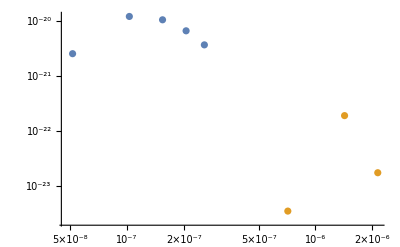

```mathematica
ListLogLogPlot[{strainSenseVfreq10yr[[175]],strainSenseVfreq10yr[[698]]}]
```

```mathematica
{xdata, ydata}= Transpose[ strainSenseVfreq10yr[[698]]   ];
```

```mathematica
xdata[[1;;3]]
```

{7.135×10^-7,1.427×10^-6,2.1405×10^-6}

```mathematica
ynewdata = ydata/√secsYear;
```

```mathematica
ynewdata[[1;;3]]
```

{6.16173×10^-28,3.38988×10^-26,3.08309×10^-27}

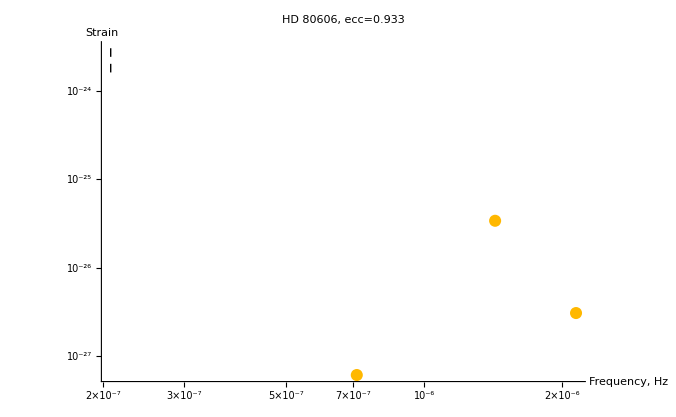

```mathematica
zplot =Show[
ListLogLogPlot[ Transpose[{xdata,ynewdata}], PlotStyle->{Hue[1.12]},PlotLabel->"HD 80606, ecc=0.933", AxesLabel->{"Frequency, Hz","Strain"}],
Graphics[{Black, Line[{{Log[2.079 10^-7], Log[1.6 10^-24]},{Log[2.079 10^-7],Log[ 2 10^-24]}}],
Line[{{Log[2.079 10^-7], Log[2.4 10^-24]},{Log[2.079 10^-7],Log[3 10^-24]}}]   }],PlotRange->All
   ]   (* {{2 10^-7, 10^-24},{2 10^-7, 3 10^-24}}  *)
```

```mathematica
Export["HD80606ecc10yr.png",zplot,"PNG", ImageSize->{11,8.5}*72]
```

HD80606ecc10yr.png

## Period decay and periastron shift for whole confirmed planet dbase.

```mathematica
{Head[cols], Keys[cols], Length[bdata]}
```

{Association,{pl_hostname,pl_letter,pl_discmethod,pl_orbper,pl_orbsmax,pl_orbeccen,pl_bmassj,st_dist,st_mass,rowupdate,st_plx},766}

```mathematica
myωDot3=Module[{amtot},
amtot=Table[bdata[[i,cols["st_mass"] ]] +bdata[[i,cols["pl_bmassj"] ]]*massJs, {i, 1, Length[bdata]}];
Table[
{bdata[[i,cols["pl_hostname"] ]],bdata[[i,cols["pl_letter"]]],bdata[[i,cols["pl_discmethod"] ]],aa=Subscript[ωdot, WT] /. { G->bigG,c->cee,M->amtot[[i]]*massSun, e->bdata[[i,cols["pl_orbeccen"] ]], Subscript[P, b]->bdata[[i,cols["pl_orbper"] ]]*secsDay},aa*secsYear*180./π , amtot[[i]], bdata[[i,cols["st_mass"] ]], bdata[[i,cols["pl_bmassj"] ]], bdata[[i,cols["pl_orbper"] ]],bdata[[i,cols["pl_orbeccen"] ]]},
{i, 1, Length[bdata]}
]
];
{{"name", "planet","discovery method", "ωdot (s/s)", "deg/year", "tot mass", "st_mass", "pl_bmassj", "pl_orbper","pl_orbeccen"}}~Join~myωDot3[[1;;3]]//TableForm
```

name | planet | discovery method | ωdot (s/s) | deg/year | tot mass | st_mass | pl_bmassj | pl_orbper | pl_orbeccen
HD 142022 A | b | Radial Velocity | 5.10841×10^-16 | 9.23635×10^-7 | 0.994869 | 0.99 | 5.1 | 1928. | 0.53
HD 39091 | b | Radial Velocity | 5.58253×10^-16 | 1.00936×10^-6 | 1.10981 | 1.1 | 10.27 | 2151. | 0.6405
HD 137388 A | b | Radial Velocity | 7.25946×10^-15 | 0.0000131256 | 0.860213 | 0.86 | 0.223 | 330. | 0.36

```mathematica
{Length[myωDot3],myωDot3[[1,4]],myωDot3[[1]]}
```

{766,5.10841×10^-16,{HD 142022 A,b,Radial Velocity,5.10841×10^-16,9.23635×10^-7,0.994869,0.99,5.1,1928.,0.53}}

```mathematica
myωDot3sort=Sort[ myωDot3, (#1[[4]]>#2[[4]])&];
{{"name", "planet","discovery method", "ωdot (rads/s)", "deg/year", "tot mass", "st_mass", "pl_bmassj", "pl_orbper", "pl_orbeccen"}}~Join~myωDot3sort[[1;;6]]//TableForm
```

name | planet | discovery method | ωdot (rads/s) | deg/year | tot mass | st_mass | pl_bmassj | pl_orbper | pl_orbeccen
PSR J1719-1438 | b | Pulsar Timing | 7.55502×10^-9 | 13.66 | 1.40115 | 1.4 | 1.2 | 0.0907063 | 0.06
WASP-19 | b | Transit | 1.52494×10^-10 | 0.27572 | 0.901021 | 0.9 | 1.069 | 0.788839 | 0.002
WASP-18 | b | Transit | 1.44266×10^-10 | 0.260844 | 1.28996 | 1.28 | 10.43 | 0.941453 | 0.0092
CoRoT-7 | b | Transit | 1.34594×10^-10 | 0.243355 | 0.910017 | 0.91 | 0.018 | 0.853592 | 0.
WASP-43 | b | Transit | 1.08218×10^-10 | 0.195666 | 0.581699 | 0.58 | 1.78 | 0.813475 | 0.
KELT-1 | b | Transit | 9.66848×10^-11 | 0.174813 | 1.346 | 1.32 | 27.23 | 1.21751 | 0.0099

```mathematica
{massE, massJ, massJe, massJs, 1/massJs}
```

{5.97×10^24,1.9×10^27,317.9,0.000954774,1047.37}

```mathematica
Subscript[ωdot, WT]
```

(6 2^(2/3) (G M)^(2/3) π^(5/3))/(c^2 (1-e^2) P_b^(5/3))